```mathematica
SetDirectory[DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]]]
```

/Users/ttesileanu/Documents/research/bio/crispr/crispr_fitness

# Matching experimental spacer abundances to spacer effectiveness or acquisition rate

In order to take advantage of intuition from actual data, it’s easiest to keep the model quantities expressed in real units. In this notebook I assume the following:
* time t is measured in hours
* bacterial and viral concentrations n_i, v are expressed in 10^8 individuals/ml
* the encounter rate g is expressed in units of 10^-8ml/hour
* fitness f is expressed in hour^-1
* spacer loss rate k is expressed in hour^-1
* death+acquisition rate of infected bacteria μ is expressed in hour^-1
* acquisition probabilities α are dimensionless (they show what fraction of the infected bacteria that are lost per unit time acquire spacers)
* the burst factor b is dimensionless
* failure probabilities η_i are dimensionless

## Set up the general equations (called automatically on init)

We write down the equations for a population of bacteria with either no spacer or a single spacer, in which both acquisition rate and effectiveness can vary between different spacers. Infected bacteria do not die instantly, but switch to a non-growing state with a constant death rate. Serial dilution and viral decay are also possible.

```mathematica
createEquationsGeneral[rules_]:=Module[{nsp=Evaluate[nsp/.rules]},
({
n[0]'[t]==f[0] (1-ntot/Kpop)n[0][t]+k Sum[n[i][t],{i,1,nsp}]-g η[0]v[t]n[0][t]-s[0]n[0][t],
nI[0]'[t]==g η[0] v[t]n[0][t]-μ nI[0][t]-s[0]nI[0][t],
v'[t]==b μ((1-αtot)nI[0][t]+ Sum[nI[k][t],{k,1,nsp}])-g v[t]Sum[n[k][t],{k,0,nsp}]-sv v[t]
}~Join~Table[
n[i]'[t]==f[i](1-ntot/Kpop)n[i][t]-k n[i][t]+μ α[i]nI[0][t]-g η[i] v[t] n[i][t]-s[i]n[i][t]
,{i,1,nsp}]~Join~
Table[
nI[i]'[t]==g η[i] v[t] n[i][t]-μ nI[i][t]-s[i]nI[i][t],
{i,1,nsp}])/.{αtot->Sum[α[i],{i,1,nsp}],ntot->Sum[n[i][t]+nI[i][t],{i,0,nsp}]}]/.rules;
```

```mathematica
createEquations[rules_]:=createEquationsGeneral[Join[rules,Append[ Table[s[i]->0,{i,0,(nsp/.rules)}],sv->0]]];
```

## Look at single spacer dynamics

Simple test

```mathematica
sampleRules1={nsp->1,f[0]->1,f[1]->0.8,b->100,μ->1,k->0.002,η[0]->1,η[1]->0.0098,g->0.0001,α[1]->0.0001,Kpop->10^5,tmax->1000};
sampleIC1={n[0][0]==10^3,n[1][0]==0,v[0]==2 10^3,nI[0][0]==0,nI[1][0]==0};
```

```mathematica
eqns=createEquations[sampleRules1]~Join~sampleIC1;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.sampleRules1)}]]~Join~{v}],{t,0,(tmax/.sampleRules1)}];
```

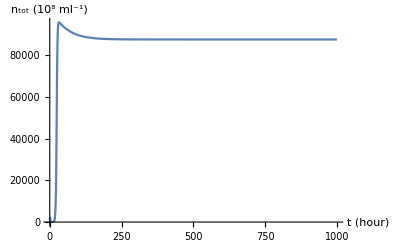

```mathematica
Plot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRules1)}]]/.soln,{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

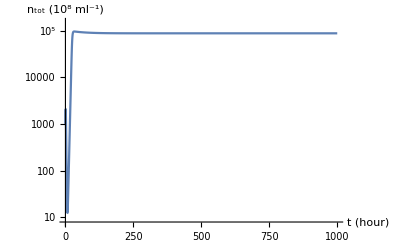

```mathematica
LogPlot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRules1)}]]/.soln,{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

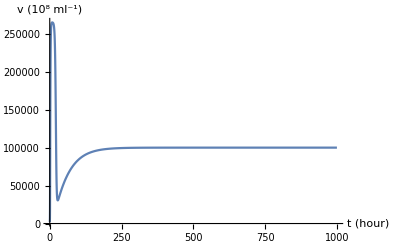

```mathematica
Plot[v[t]/.soln,{t,0,(tmax/.sampleRules1)},AxesLabel->{"t (hour)", "v (10^8 ml^-1)"},PlotRange->All]
```

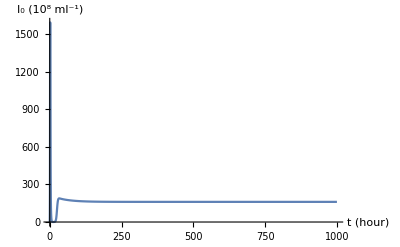

```mathematica
Plot[nI[0][t]/.soln,{t,0,(tmax/.sampleRules1)},AxesLabel->{"t (hour)", "I_0 (10^8 ml^-1)"},PlotRange->All]
```

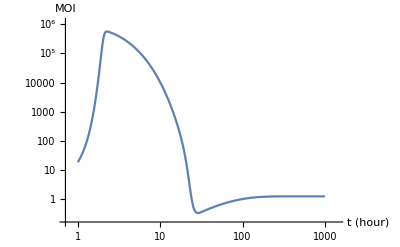

```mathematica
LogLogPlot[(v[t]/(n[0][t]+n[1][t]))/.soln,{t,1,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "MOI"}]
```

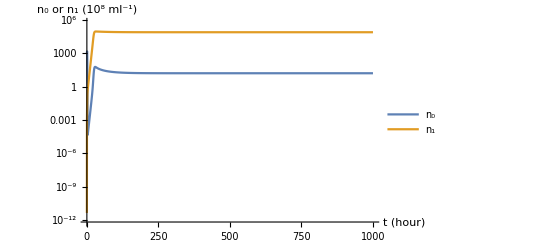

```mathematica
LogPlot[Evaluate[{n[0][t],n[1][t]}/.soln],{t,0,(tmax/.sampleRules1)},PlotRange->All,AxesLabel->{"t (hour)", "n_0 or n_1 (10^8 ml^-1)"},PlotLegends->{"n_0","n_1"}]
```

Test dynamics without infected cells

```mathematica
sampleRules2={nsp->1,f[0]->1,f[1]->0.8, b->50,k->0.001,η[0]->1,η[1]->0.0011,g->0.00001,α[1]->0.0001,Kpop->10^5,tmax->24};
sampleIC2={n[0][0]==10^4,n[1][0]==0,v[0]==10^4};
```

Some Mathematica ninja: remove the references to the infected cells, replacing them by the appropriate expression in the μ→∞ limit.

```mathematica
eqns=(Select[Normal[Series[createEquations[{nsp->1}]/.nI[k_][t]->g η[k] v[t]n[k][t]/μ,{μ,Infinity,0}]],!MatchQ[#[[1]],nI[_]'[_]]&]/.sampleRules2)~Join~sampleIC2;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Table[n[k],{k,0,(nsp/.sampleRules2)}]~Join~{v}],{t,0,(tmax/.sampleRules2)}];
```

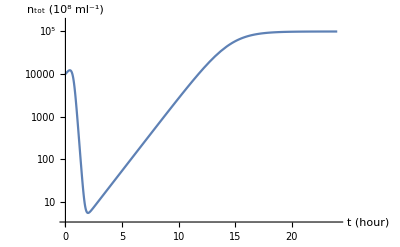

```mathematica
LogPlot[Evaluate[Sum[n[k][t],{k,0,(nsp/.sampleRules2)}]]/.soln,{t,0,(tmax/.sampleRules2)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

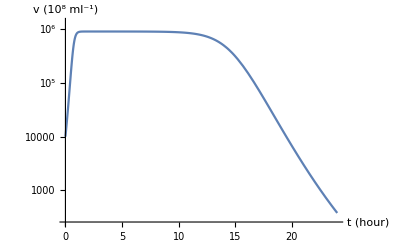

```mathematica
LogPlot[v[t]/.soln,{t,0,(tmax/.sampleRules2)},AxesLabel->{"t (hour)", "v (10^8 ml^-1)"}]
```

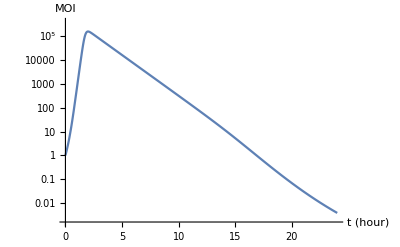

```mathematica
LogPlot[(v[t]/(n[0][t]+n[1][t]))/.soln,{t,0,(tmax/.sampleRules2)},PlotRange->All,AxesLabel->{"t (hour)", "MOI"}]
```

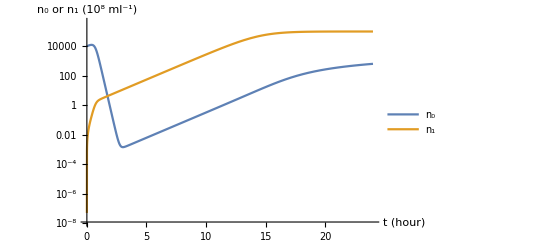

```mathematica
LogPlot[Evaluate[{n[0][t],n[1][t]}/.soln],{t,0,(tmax/.sampleRules2)},PlotRange->All,AxesLabel->{"t (hour)", "n_0 or n_1 (10^8 ml^-1)"},PlotLegends->{"n_0","n_1"}]
```

MOI increased by wildtype

Let’s first focus on experiments in which we have a mixture of wildtype and bacteria with a single spacer, and acquisition is disabled. The wildtype bacteria are useful for (temporarily) increasing the MOI, thus providing a challenge for the effectiveness of the spacer.

How much does the time at which the bacterial population start growing exponentially depend on the spacer effectiveness?

```mathematica
Clear[tmax];
noAcqDefaultRules={nsp->1,f[_]->2,b->50,μ->1,k->0.00,g->0.05,α[1]->0.00,Kpop->10^2,tmax->24,η[0]->1};
noAcqDefaultIC={n[0][0]==10^0,n[1][0]==10^(-4),v[0]==10^1,nI[0][0]==0,nI[1][0]==0};
```

```mathematica
noAcqGenerateAndSolve::usage="noAcqGenerateAndSolve[ϵvalues]
noAcqGenerateAndSolve[ηvalues,overrides]

This function generates the equations for a simulation of a mixture of wildtype bacteria with single-spacer bacteria and virus, with acquisition disabled. The second form of the command allows to override some of the default options.

The function runs one simulation for each entry in ϵvalues, representing the failure rate of the spacer. The return value contains three elements: {solns, eqns, rules}.

The first one is a list of results of NDSolve, giving the solutions for each value of η.

The second one contains the equations that are solved, in which the spacer effectiveness is left unreplaced.

The third one contains the list of rules used in the simulation, including the overrides.";
noAcqGenerateAndSolve[ηvalues_List,overrides_:{} ]:=Module[
{overridden,notoverridden,currentrules,eqns0,varlist,tmax0},
overridden=(overrides/.(A_->B_)->A);
notoverridden=Select[noAcqDefaultRules,!MemberQ[overridden, #[[1]]]&];
currentrules=notoverridden~Join~overrides;
eqns0=createEquations[currentrules]~Join~noAcqDefaultIC;
tmax0=(tmax/.currentrules);
varlist=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.currentrules)}]]~Join~{v};
solns=Map[
NDSolve[Evaluate[eqns0/.η[1]->#],varlist,{t,0,tmax0}]&,ηvalues];
{solns,eqns0,currentrules}
];
```

```mathematica
ηtotest={0.0001, 0.012, 0.02, 0.03};
ηdependence=noAcqGenerateAndSolve[ηtotest,{tmax->16}];
```

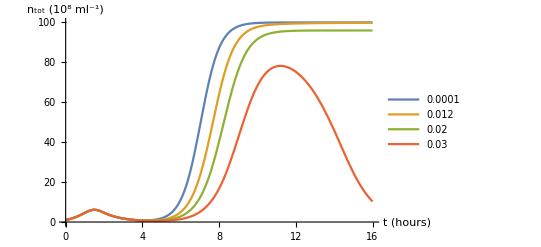

```mathematica
Plot[Evaluate[n[0][t]+n[1][t]+nI[0][t]+nI[1][t]/.ηdependence[[1]]],{t,0,(tmax/.ηdependence[[3]])},AxesLabel->{"t (hours)", "n_tot (10^8 ml^-1)"},PlotLegends->Evaluate[ηtotest]]
```

Paper examples

### Fig. 3a, b

```mathematica
createEquations[{nsp->1}]
```

{n[0]'[t]==-g v[t] η[0] n[0][t]+k n[1][t]+f[0] n[0][t] (1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop),nI[0]'[t]==g v[t] η[0] n[0][t]-μ nI[0][t],v'[t]==-g v[t] (n[0][t]+n[1][t])+b μ ((1-α[1]) nI[0][t]+nI[1][t]),n[1]'[t]==-k n[1][t]-g v[t] η[1] n[1][t]+μ α[1] nI[0][t]+f[1] n[1][t] (1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop),nI[1]'[t]==g v[t] η[1] n[1][t]-μ nI[1][t]}

```mathematica
commonPaperRules={nsp->1,f[0]->1,b->100,μ->1,η[0]->1,g->10^-5,α[1]->0.0001,Kpop->10^5,tmax->5000};
paperRules1=Join[commonPaperRules, {f[1]->0.8,η[1]->0,k->0.002}];
paperRules2=Join[commonPaperRules, {f[1]->0.3,η[1]->0,k->0.002}];
paperRules3=Join[commonPaperRules, {f[1]->0.8,η[1]->0.0099,k->0.002}];
paperIC={n[0][0]==1000,n[1][0]==0,v[0]==10000,nI[0][0]==0,nI[1][0]==0};
```

```mathematica
1-k/f[0] 1/(1-b η[1])((1-α[1])b-1)/((b-1)+(f[1]/f[0]-1)((1-α[1])b-1)/(1-α[1]-η[1]))/.{paperRules1,paperRules2,paperRules3}
```

{0.9975,0.993334,0.749399}

```mathematica
eqns1=createEquations[paperRules1]~Join~paperIC;
eqns2=createEquations[paperRules2]~Join~paperIC;
eqns3=createEquations[paperRules3]~Join~paperIC;
```

```mathematica
soln1=NDSolve[eqns1,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.paperRules1)}]]~Join~{v}],{t,0,(tmax/.paperRules1)}];
soln2=NDSolve[eqns2,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.paperRules2)}]]~Join~{v}],{t,0,(tmax/.paperRules2)}];
soln3=NDSolve[eqns3,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.paperRules3)}]]~Join~{v}],{t,0,(tmax/.paperRules3)}];
```

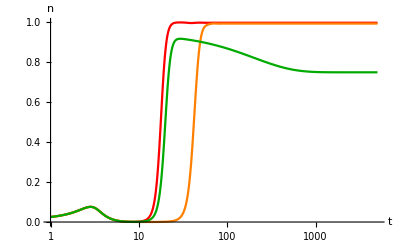

```mathematica
plot1=LogLinearPlot[Evaluate[
(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop/.{Join[soln1[[1]],paperRules1],Join[soln2[[1]],paperRules2],Join[soln3[[1]],paperRules3]}],{t,1,(tmax/.paperRules1)},PlotStyle->{Red,Orange,Darker[Green]},AxesLabel->{t,n}]
```

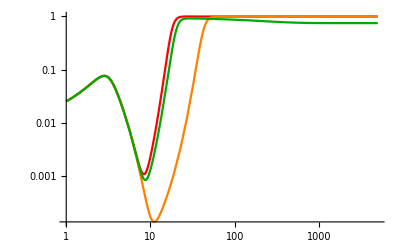

```mathematica
LogLogPlot[Evaluate[
(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop/.{Join[soln1[[1]],paperRules1],Join[soln2[[1]],paperRules2],Join[soln3[[1]],paperRules3]}],{t,1,(tmax/.paperRules1)},PlotStyle->{Red,Orange,Darker[Green]}]
```

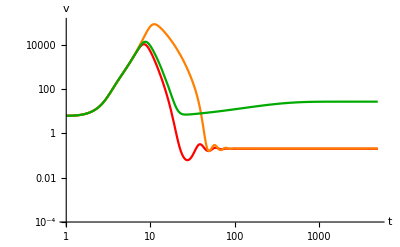

```mathematica
plot2=LogLogPlot[Evaluate[
v[t]/(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/.{Join[soln1[[1]],paperRules1],Join[soln2[[1]],paperRules2],Join[soln3[[1]],paperRules3]}],{t,1,(tmax/.paperRules1)},PlotStyle->{Red,Orange,Darker[Green]},PlotRange->{10^-4,10^5},AxesLabel->{t,v}]
```

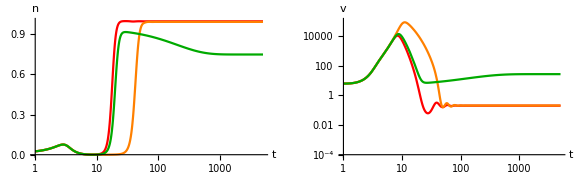

```mathematica
Show[GraphicsGrid[{{plot1,plot2}}],ImageSize->Large]
```

### Fig. 3c

```mathematica
commonRules={f[0]->1,k->0.01,b->100};
alphas=Table[0.25+i 0.1,{i,0,7}];
```

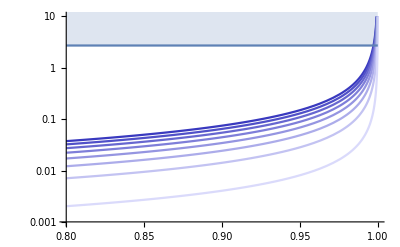

```mathematica
fFactorPlots=Function[alpha,LogPlot[k/f[0](b(1-alpha)-1)/((b-1)(1-bη))/.commonRules,{bη,0.8,1},PlotRange->{0.001,10},PlotStyle->{Blend[{Darker[Blue],Blend[{Blue,White},0.9]},alpha]}]]/@alphas;
Show[fFactorPlots~Join~{Plot[1,{bη,0.8,1},Filling->10]}]
```

### Fig. 4a, b

```mathematica
commonRules={nsp->20,f[_]->1,b->100,μ->1,η[0]->1,g->10^-4,Kpop->10^5,k->0.01,tmax->100000};
commonIC={n[0][0]==1000,v[0]==10000,nI[0][0]==0}~Join~Flatten[Table[{n[i][0]==0,nI[i][0]==0},{i,1,(nsp/.commonRules)}]];
alphaRules={α[1]->0}~Join~Table[α[i]->i/2000,{i,2,(nsp/.commonRules)}];
topChangingRules={{η[_?Positive]->0}~Join~alphaRules,{η[_?Positive]->0.0098}~Join~alphaRules,
{η[_?Positive]->0,α[_]->0.0055},{η[_?Positive]->0.0098,α[_]->0.0055}};
etaRules=Table[η[i]->(0.0098(i-1)/19),{i,1,(nsp/.commonRules)}];
bottomChangingRules={{α[_]->0.0005}~Join~etaRules,{α[_]->0.01}~Join~etaRules,{α[_]->0.045}~Join~etaRules};
topAllRules=(Join[commonRules, #]&)/@topChangingRules;
bottomAllRules=(Join[commonRules, #]&)/@bottomChangingRules;
```

```mathematica
topEqns=(createEquations[#]~Join~commonIC&)/@topAllRules;
bottomEqns=(createEquations[#]~Join~commonIC&)/@bottomAllRules;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
topSolns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{topEqns,topAllRules}];
bottomSolns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{bottomEqns,bottomAllRules}];
```

```mathematica
ntotRule={ntot[t_]->Sum[n[i][t],{i,1,(nsp/.commonRules)}]+Sum[nI[i][t],{i,1,(nsp/.commonRules)}]};
topFinalFracs=(Table[n[i][(tmax/.commonRules)]/ntot[(tmax/.commonRules)]/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@topSolns;
bottomFinalFracs=(Table[n[i][(tmax/.commonRules)]/ntot[(tmax/.commonRules)]/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@bottomSolns;
```

```mathematica
alphaValues=alphaRules/.(α[_]->x_)->x;
etaValues=etaRules/.(η[_]->x_)->x;
```

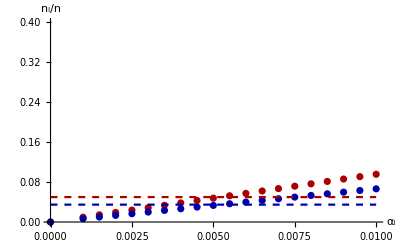

```mathematica
Show[ListPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[1]]}]],PlotStyle->Darker[Red]],ListPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[2]]}]],PlotStyle->Darker[Blue]],
ListPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[3]]}]],Joined->True,PlotStyle->{Darker[Red],Dashed}],
ListPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[4]]}]],Joined->True,PlotStyle->{Darker[Blue],Dashed}],PlotRange->{0,0.4},AxesLabel->{Subscript[α, i],Subscript[n, i]/n}]
```

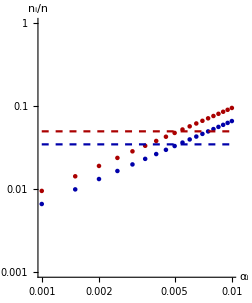

```mathematica
Show[ListLogLogPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[1]]}]],PlotStyle->Darker[Red]],ListLogLogPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[2]]}]],PlotStyle->Darker[Blue]],
ListLogLogPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[3]]}]],Joined->True,PlotStyle->{Darker[Red],Dashed}],
ListLogLogPlot[Evaluate[Transpose[{alphaValues,topFinalFracs[[4]]}]],Joined->True,PlotStyle->{Darker[Blue],Dashed}],PlotRange->Log[{0.001,1}],AxesLabel->{Subscript[α, i],Subscript[n, i]/n},AspectRatio->1.2]
```

```mathematica
(*bottomFinalFracs=(Table[n[i][tmax]/ntot[tmax]/.tmax->800/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@bottomSolns;*)
```

```mathematica
plot1Dots=ListPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[1]]}]],PlotStyle->Darker[Red],PlotRange->All];
plot1Lines=ListPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[1]]}]],PlotStyle->{Dashed,Darker[Red]},PlotRange->All,Joined->True];
```

```mathematica
plot2Dots=ListPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[2]]}]],PlotStyle->Lighter[Blue],PlotRange->All];
plot2Lines=ListPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[2]]}]],PlotStyle->{Dashed,Lighter[Blue]},PlotRange->All,Joined->True];
```

```mathematica
plot3Dots=ListPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[3]]}]],PlotStyle->Darker[Blue],PlotRange->All];
plot3Lines=ListPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[3]]}]],PlotStyle->{Dashed,Darker[Blue]},PlotRange->All,Joined->True];
```

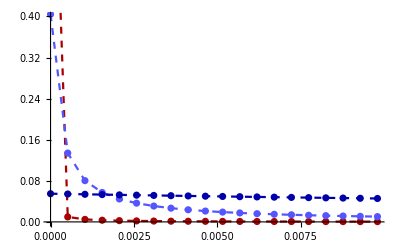

```mathematica
Show[plot1Lines,plot2Lines,plot3Lines,plot1Dots,plot2Dots,plot3Dots,PlotRange->{0,0.4}]
```

```mathematica
logPlot1Dots=ListLogPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[1]]}]],PlotStyle->Darker[Red],PlotRange->All];
logPlot1Lines=ListLogPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[1]]}]],PlotStyle->{Dashed,Darker[Red]},PlotRange->All,Joined->True];
```

```mathematica
logPlot2Dots=ListLogPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[2]]}]],PlotStyle->Lighter[Blue],PlotRange->All];
logPlot2Lines=ListLogPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[2]]}]],PlotStyle->{Dashed,Lighter[Blue]},PlotRange->All,Joined->True];
```

```mathematica
logPlot3Dots=ListLogPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[3]]}]],PlotStyle->Darker[Blue],PlotRange->All];
logPlot3Lines=ListLogPlot[Evaluate[Transpose[{etaValues,bottomFinalFracs[[3]]}]],PlotStyle->{Dashed,Darker[Blue]},PlotRange->All,Joined->True];
```

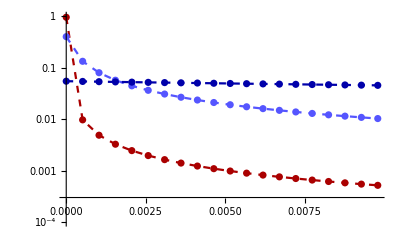

```mathematica
Show[logPlot1Lines,logPlot2Lines,logPlot3Lines,logPlot1Dots,logPlot2Dots,logPlot3Dots,PlotRange->Log[{0.0001,1}]]
```

### Fig. 4c

```mathematica
commonRules={nsp->20,f[_]->1,b->100,μ->1,η[0]->1,g->10^-4,Kpop->10^5,k->0.01,tmax->100000};
commonIC={n[0][0]==1000,v[0]==10000,nI[0][0]==0}~Join~Flatten[Table[{n[i][0]==0,nI[i][0]==0},{i,1,(nsp/.commonRules)}]];
alphaRules=Table[α[i]->i 15/20000,{i,1,(nsp/.commonRules)}];
etaRules=Table[η[i]->(0.0098(i-1)/19),{i,1,(nsp/.commonRules)}];
changingRules={Flatten[{alphaRules,etaRules}],Flatten[{alphaRules/.(α[A_]->α[(nsp-A+1)/.commonRules]),etaRules}],
{α[_]->0.007875}~Join~etaRules};
allRules=(Join[commonRules, #]&)/@changingRules;
```

```mathematica
allEqns=(createEquations[#]~Join~commonIC&)/@allRules;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
solns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{allEqns,allRules}];
```

```mathematica
ntotRule={ntot[t_]->Sum[n[i][t],{i,1,(nsp/.commonRules)}]+Sum[nI[i][t],{i,1,(nsp/.commonRules)}]};
etaValues=etaRules/.(η[_]->x_)->x;
finalFracs=(Table[n[i][tmax]/ntot[tmax](*/.tmax->1000*)/.commonRules/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@solns;
```

```mathematica
pltRange={0.0005,0.8};
```

```mathematica
plot1Joined=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracs[[1]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Red]];
plot1Dots=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.6alphaValues[[i[[1]]]]/Max[alphaValues]]])],Transpose[{etaValues,finalFracs[[1]]}]]],PlotRange->pltRange];
```

```mathematica
plot2Joined=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracs[[2]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Blue]];
plot2Dots=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.6alphaValues[[-i[[1]]]]/Max[alphaValues]]])],Transpose[{etaValues,finalFracs[[2]]}]]],PlotRange->pltRange];
```

```mathematica
plot3Joined=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracs[[3]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Green]];
plot3Dots=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.60 .007875/Max[alphaValues]]])],Transpose[{etaValues,finalFracs[[3]]}]]],PlotRange->pltRange];
```

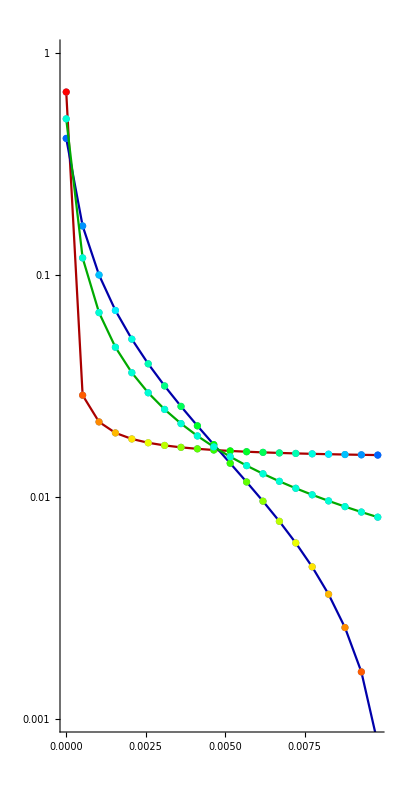

```mathematica
Show[plot1Joined,plot1Dots,plot2Joined,plot2Dots,plot3Joined,plot3Dots,PlotRange->Log[{0.001, 1}],AspectRatio->2]
```

### SI Fig. 1

```mathematica
commonRules={nsp->1,f[0]->1,f[1]->1,b->100,μ->1,η[0]->1,η[1]->0,g->10^-5,Kpop->10^5,tmax->1000};
commonIC={n[0][0]==1000,n[1][0]==0,v[0]==10000,nI[0][0]==0,nI[1][0]==0};
leftChangingRules=Table[{α[1]->0.003 i,k->0.001,idx->i},{i,1,10}];
rightChangingRules=Table[{k->0.00035i,α[1]->0.003,idx->i},{i,1,10}];
leftAllRules=(Join[commonRules, #]&)/@leftChangingRules;
rightAllRules=(Join[commonRules, #]&)/@rightChangingRules;
```

```mathematica
leftEqns=(createEquations[#]~Join~commonIC&)/@leftAllRules;
rightEqns=(createEquations[#]~Join~commonIC&)/@rightAllRules;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
leftSolns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{leftEqns,leftAllRules}];
rightSolns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{rightEqns,rightAllRules}];
```

```mathematica
leftPlotsWildtype=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[n[0][t]/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{leftSolns,leftAllRules}];
```

```mathematica
leftPlotsWildtypeAll=Show[leftPlotsWildtype,AxesLabel->{t,Subscript[n, 0]}];
```

```mathematica
leftPlotsInfected=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[(nI[0][t](*+nI[1][t]*))/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{leftSolns,leftAllRules}];
```

```mathematica
leftPlotsInfectedAll=Show[leftPlotsInfected,AxesLabel->{t,"infected"}];
```

```mathematica
leftPlotsTotal=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/(Kpop/.rules)/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{leftSolns,leftAllRules}];
```

```mathematica
leftPlotsTotalAll=Show[leftPlotsTotal,AxesLabel->{t,"n/K"}];
```

```mathematica
leftPlotsMOI=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[v[t]/(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{leftSolns,leftAllRules}];
```

```mathematica
leftPlotsMOIAll=Show[leftPlotsMOI,AxesLabel->{t,"MOI"}];
```

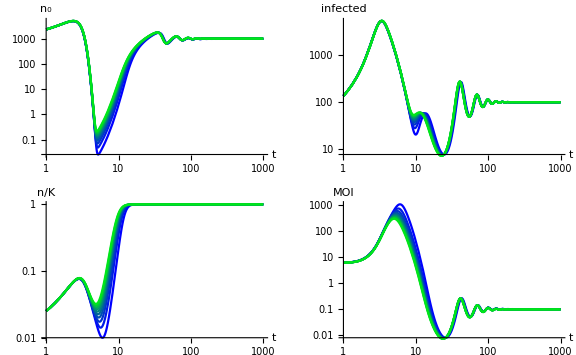

```mathematica
GraphicsGrid[{{leftPlotsWildtypeAll,leftPlotsInfectedAll},{leftPlotsTotalAll,leftPlotsMOIAll}},ImageSize->Large]
```

```mathematica
rightPlotsWildtype=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[n[0][t]/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{rightSolns,rightAllRules}];
```

```mathematica
rightPlotsWildtypeAll=Show[rightPlotsWildtype,AxesLabel->{t,Subscript[n, 0]}];
```

```mathematica
rightPlotsInfected=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[(nI[0][t](*+nI[1][t]*))/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{rightSolns,rightAllRules}];
```

```mathematica
rightPlotsInfectedAll=Show[rightPlotsInfected,AxesLabel->{t,"infected"}];
```

```mathematica
rightPlotsTotal=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/(Kpop/.rules)/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{rightSolns,rightAllRules}];
```

```mathematica
rightPlotsTotalAll=Show[rightPlotsTotal,AxesLabel->{t,"n/K"}];
```

```mathematica
rightPlotsMOI=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[v[t]/(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{rightSolns,rightAllRules}];
```

```mathematica
rightPlotsMOIAll=Show[rightPlotsMOI,AxesLabel->{t,"MOI"}];
```

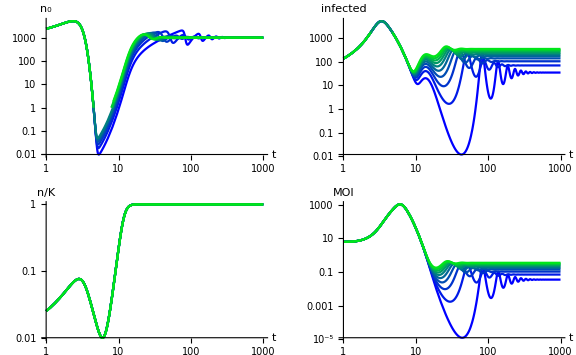

```mathematica
GraphicsGrid[{{rightPlotsWildtypeAll,rightPlotsInfectedAll},{rightPlotsTotalAll,rightPlotsMOIAll}},ImageSize->Large]
```

### SI Fig. 2

```mathematica
commonRules={nsp->1,f[0]->1,f[1]->1,b->100,μ->1,η[0]->1,g->10^-5,Kpop->10^5,tmax->1000,k->0.002,α[1]->0.003};
commonIC={n[0][0]==1000,n[1][0]==0,v[0]==10000,nI[0][0]==0,nI[1][0]==0};
changingRules={{η[1]->0,idx->1}}~Join~Table[{η[1]->0.00099 i,idx->i},{i,2,10}];
allRules=(Join[commonRules, #]&)/@changingRules;
```

```mathematica
allEqns=(createEquations[#]~Join~commonIC&)/@allRules;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
solns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{allEqns,allRules}];
```

```mathematica
plotsWildtype=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[n[0][t]/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{solns,allRules}];
```

```mathematica
plotsWildtypeAll=Show[plotsWildtype,AxesLabel->{t,Subscript[n, 0]}];
```

```mathematica
plotsInfected=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[(nI[0][t](*+nI[1][t]*))/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]},PlotRange->{0.1,10000}]],{solns,allRules}];
```

```mathematica
plotsInfectedAll=Show[plotsInfected,AxesLabel->{t,"infected"}];
```

```mathematica
plotsTotal=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/(Kpop/.rules)/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{solns,allRules}];
```

```mathematica
plotsTotalAll=Show[plotsTotal,AxesLabel->{t,"n/K"}];
```

```mathematica
plotsMOI=MapThread[Function[{soln,rules},LogLogPlot[Evaluate[v[t]/(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/.soln[[1]]],{t,1,(tmax/.rules)},PlotStyle->{Blend[{Blue,Green},(idx-1)/10/.rules]}]],{solns,allRules}];
```

```mathematica
plotsMOIAll=Show[plotsMOI,AxesLabel->{t,"MOI"}];
```

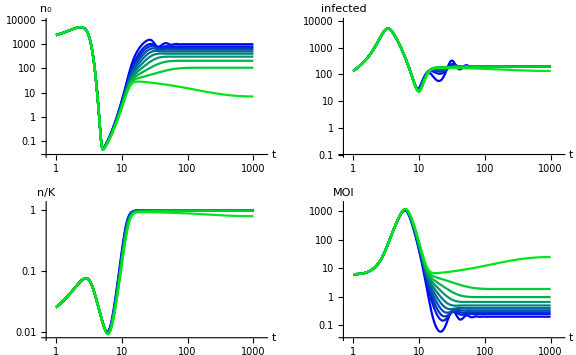

```mathematica
GraphicsGrid[{{plotsWildtypeAll,plotsInfectedAll},{plotsTotalAll,plotsMOIAll}},ImageSize->Large]
```

### SI Fig. 3

```mathematica
commonRules={nsp->1,f[0]->1,b->0,μ->0,η[0]->0,η[1]->0,g->0,Kpop->10^5,tmax->1000,k->0.01,α[1]->0};
commonIC={n[0][0]==50,n[1][0]==50,v[0]==0,nI[0][0]==0,nI[1][0]==0};
changingRules=Table[{f[1]->0.3 i,idx->i},{i,1,5}];
allRules=(Join[commonRules, #]&)/@changingRules;
rulesSpecial=Join[commonRules,{f[1]->1}];
```

```mathematica
eqns=(createEquations[#]~Join~commonIC&)/@allRules;
eqnsSpecial=createEquations[rulesSpecial]~Join~commonIC;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
solns=MapThread[Function[{eqn,rules},
NDSolve[eqn,vars,{t,0,(tmax/.rules)}]],{eqns,allRules}];
solnSpecial=NDSolve[eqnsSpecial,vars,{t,0,(tmax/.commonRules)}];
```

```mathematica
plots=MapThread[Function[{soln,rules},Plot[Evaluate[n[1][t]/(n[0][t]+n[1][t])/.soln[[1]]],{t,0,(tmax/5/.commonRules)},PlotRange->All,PlotStyle->{Thin,Blend[{Green,Black},((idx-1)/5/.rules)]}]],{solns, allRules}];
plotSpecial=Plot[Evaluate[n[1][t]/(n[0][t]+n[1][t])/.solnSpecial[[1]]],{t,0,(tmax/5/.commonRules)},PlotStyle->{Black,Thick}];
```

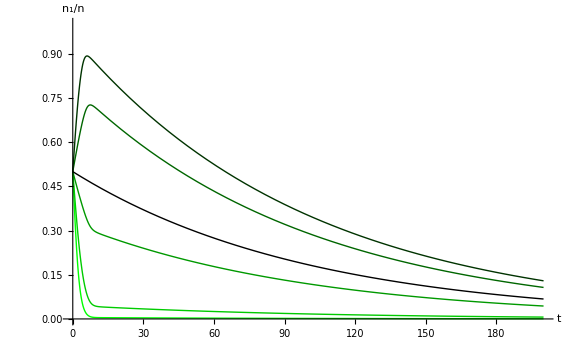

```mathematica
Show[plots~Join~{plotSpecial},PlotRange->{0,1},AxesLabel->{t,"n_1/n"},ImageSize->Large]
```

```mathematica
logPlots=MapThread[Function[{soln,rules},LogPlot[Evaluate[n[1][t]/(n[0][t]+n[1][t])/.soln[[1]]],{t,0,(tmax/.commonRules)},PlotRange->All,PlotStyle->{Thin,Blend[{Green,Black},((idx-1)/5/.rules)]}]],{solns, allRules}];
logPlotSpecial=LogPlot[Evaluate[n[1][t]/(n[0][t]+n[1][t])/.solnSpecial[[1]]],{t,0,(tmax/.commonRules)},PlotStyle->{Black,Thick}];
```

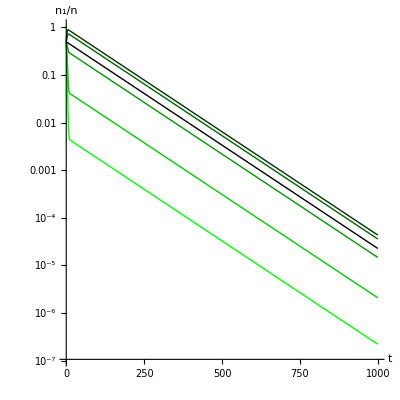

```mathematica
Show[logPlots~Join~{logPlotSpecial},AxesLabel->{t,"n_1/n"},AspectRatio->1]
```

### SI Fig. 4

```mathematica
nRuns=10;
commonRules={nsp->100,f[_]->1,b->100,μ->1,η[0]->1,g->10^-4,Kpop->10^5,k->0.01,tmax->100000};
commonIC={n[0][0]==1000,v[0]==10000,nI[0][0]==0}~Join~Flatten[Table[{n[i][0]==0,nI[i][0]==0},{i,1,(nsp/.commonRules)}]];
alphaValuesBottom=Table[Table[RandomReal[{0.00015,0.0020}],{i,1,(nsp/.commonRules)}],{j,1,nRuns}];
alphaValuesTop=Table[Table[RandomReal[{0.003,0.005}],{i,1,(nsp/.commonRules)}],{j,1,nRuns}];
etaValuesBottom=Table[Table[RandomReal[{0,0.0098}],{i,1,(nsp/.commonRules)}],{j,1,nRuns}];
etaValuesTop=Table[Table[RandomReal[{0,0.0098}],{i,1,(nsp/.commonRules)}],{j,1,nRuns}];
```

```mathematica
allRulesBottom=MapThread[Function[{crtAlphas,crtEtas},Join[commonRules,Flatten[MapIndexed[Function[{pair,i},{α[i[[1]]]->pair[[1]],η[i[[1]]]->pair[[2]]}],Transpose[{crtAlphas,crtEtas}]]]]],{alphaValuesBottom, etaValuesBottom}];
allRulesTop=MapThread[Function[{crtAlphas,crtEtas},Join[commonRules,Flatten[MapIndexed[Function[{pair,i},{α[i[[1]]]->pair[[1]],η[i[[1]]]->pair[[2]]}],Transpose[{crtAlphas,crtEtas}]]]]],{alphaValuesTop,etaValuesTop}];
```

```mathematica
eqnsBottom=(createEquations[#]~Join~commonIC&)/@allRulesBottom;
eqnsTop=(createEquations[#]~Join~commonIC&)/@allRulesTop;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
solnsBottom=(NDSolve[Evaluate[#],vars,{t,0,Evaluate[(tmax/.commonRules)]}]&)/@eqnsBottom;
solnsTop=(NDSolve[Evaluate[#],vars,{t,0,Evaluate[(tmax/.commonRules)]}]&)/@eqnsTop;
```

```mathematica
ntotRule={ntot[t_]->Sum[n[i][t],{i,1,(nsp/.commonRules)}]+Sum[nI[i][t],{i,1,(nsp/.commonRules)}]};
bottomFinalFracs=(Table[n[i][tmax]/ntot[tmax]/.commonRules/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@solnsBottom;
topFinalFracs=(Table[n[i][tmax]/ntot[tmax]/.commonRules/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@solnsTop;
```

```mathematica
bottomFinalFracsFlat=Flatten[bottomFinalFracs];
topFinalFracsFlat=Flatten[topFinalFracs];
alphaValuesBottomFlat=Flatten[alphaValuesBottom];
alphaValuesTopFlat=Flatten[alphaValuesTop];
etaValuesBottomFlat=Flatten[etaValuesBottom];
etaValuesTopFlat=Flatten[etaValuesTop];
```

```mathematica
colorFunction[x_]:=ColorData["SunsetColors"][x];
```

```mathematica
(*colorFunction[x_]:=Blend[{Darker[Purple],Orange,Yellow}, x];*)
```

```mathematica
plotTop=ListPlot[MapIndexed[Function[{pair,i},Style[pair,colorFunction[topFinalFracsFlat[[i[[1]]]]/(*0.045*)0.08]]],Transpose[{etaValuesTopFlat,alphaValuesTopFlat}]],PlotStyle->{PointSize[Large]}];
```

```mathematica
plotBottom=ListPlot[MapIndexed[Function[{pair,i},Style[pair,colorFunction[bottomFinalFracsFlat[[i[[1]]]]/(*0.045*)0.08]]],Transpose[{etaValuesBottomFlat,alphaValuesBottomFlat}]],PlotStyle->{PointSize[Large]}];
```

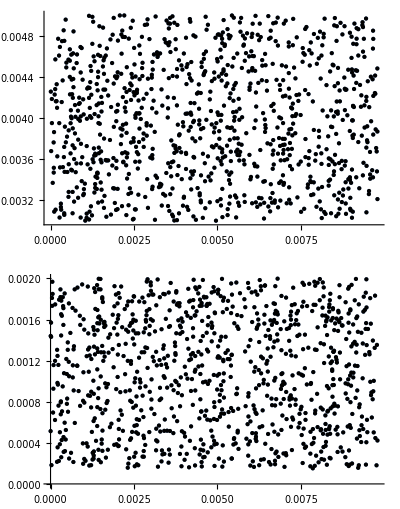

```mathematica
Legended[GraphicsGrid[{{plotTop},{plotBottom}}],BarLegend[{"SunsetColors",{0,(*0.045*)0.08}},LegendMargins->0,LegendMarkerSize->400]]
```

```mathematica
(*Export["tmp.pdf",plotBottom,"PDF"]*)
```

```mathematica
(*Export["SI_Fig4_top.csv",Transpose[{etaValuesTopFlat,alphaValuesTopFlat,topFinalFracsFlat}]]*)
```

```mathematica
(*Export["SI_Fig4_bottom.csv",Transpose[{etaValuesBottomFlat,alphaValuesBottomFlat,bottomFinalFracsFlat}]]*)
```

Check convergence.

```mathematica
Map[Function[{crtSoln}, Max[Abs/@(((#'[tmax]&)/@vars)/.commonRules/.crtSoln[[1]])/((((#[tmax]&)/@vars)/.commonRules/.crtSoln[[1]]))]],solnsBottom]
```

{8.55299×10^-9,1.7956×10^-7,1.42796×10^-6,7.98699×10^-10,5.74912×10^-8,2.79888×10^-9,2.09566×10^-6,1.91297×10^-8,5.68537×10^-13,6.1552×10^-12}

```mathematica
Map[Function[{crtSoln},Max[Abs/@(((#'[tmax]&)/@vars)/.commonRules/.crtSoln[[1]])/((((#[tmax]&)/@vars)/.commonRules/.crtSoln[[1]]))]],solnsTop]
```

{1.1698×10^-19,1.81109×10^-15,3.31003×10^-19,2.68665×10^-19,1.63494×10^-19,2.82802×10^-17,1.94141×10^-19,5.06446×10^-19,2.76241×10^-19,2.10301×10^-19}

### SI Fig. 5

```mathematica
commonRules={nsp->20,f[_]->1,b->100,μ->1,η[0]->1,g->10^-4,Kpop->10^5,k->0.01,tmax->100000,tmaxEarly->1000};
commonIC={n[0][0]==1000,v[0]==10000,nI[0][0]==0}~Join~Flatten[Table[{n[i][0]==0,nI[i][0]==0},{i,1,(nsp/.commonRules)}]];
alphaRules=Table[α[i]->i 15/20000,{i,1,(nsp/.commonRules)}];
etaRules=Table[η[i]->(0.0098(i-1)/19),{i,1,(nsp/.commonRules)}];
changingRules={Flatten[{alphaRules,etaRules}],Flatten[{alphaRules/.(α[A_]->α[(nsp-A+1)/.commonRules]),etaRules}],
{α[_]->0.007875}~Join~etaRules};
allRules=(Join[commonRules, #]&)/@changingRules;
```

```mathematica
allEqns=(createEquations[#]~Join~commonIC&)/@allRules;
```

```mathematica
vars=Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.commonRules)}]~Join~{v}];
```

```mathematica
solns=MapThread[Function[{eqns,rules},
NDSolve[eqns,vars,{t,0,(tmax/.rules)}]],{allEqns,allRules}];
```

```mathematica
ntotRule={ntot[t_]->Sum[n[i][t],{i,1,(nsp/.commonRules)}]+Sum[nI[i][t],{i,1,(nsp/.commonRules)}]};
etaValues=etaRules/.(η[_]->x_)->x;
finalFracs=(Table[n[i][tmax]/ntot[tmax](*/.tmax->1000*)/.commonRules/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@solns;
finalFracsEarly=(Table[n[i][tmax]/ntot[tmax]/.tmax->tmaxEarly/.commonRules/.ntotRule,{i,1,(nsp/.commonRules)}]/.#[[1]]&)/@solns;
```

```mathematica
pltRange={0.0005,0.8};
```

```mathematica
plot1Joined=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracs[[1]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Red]];
plot1Dots=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.6alphaValues[[i[[1]]]]/Max[alphaValues]]])],Transpose[{etaValues,finalFracs[[1]]}]]],PlotRange->pltRange];
```

```mathematica
plot2Joined=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracs[[2]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Blue]];
plot2Dots=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.6alphaValues[[-i[[1]]]]/Max[alphaValues]]])],Transpose[{etaValues,finalFracs[[2]]}]]],PlotRange->pltRange];
```

```mathematica
plot3Joined=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracs[[3]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Green]];
plot3Dots=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.60 .007875/Max[alphaValues]]])],Transpose[{etaValues,finalFracs[[3]]}]]],PlotRange->pltRange];
```

```mathematica
plot1JoinedEarly=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracsEarly[[1]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Red]];
plot1DotsEarly=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.6alphaValues[[i[[1]]]]/Max[alphaValues]]])],Transpose[{etaValues,finalFracsEarly[[1]]}]]],PlotRange->pltRange];
```

```mathematica
plot2JoinedEarly=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracsEarly[[2]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Blue]];
plot2DotsEarly=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.6alphaValues[[-i[[1]]]]/Max[alphaValues]]])],Transpose[{etaValues,finalFracsEarly[[2]]}]]],PlotRange->pltRange];
```

```mathematica
plot3JoinedEarly=ListLogPlot[Evaluate[Transpose[{etaValues,finalFracsEarly[[3]]}]],PlotRange->pltRange,Joined->True,PlotStyle->Darker[Green]];
plot3DotsEarly=ListLogPlot[Evaluate[MapIndexed[Function[{pair,i},(Style[{pair[[1]],pair[[2]]},Hue[0.60 .007875/Max[alphaValues]]])],Transpose[{etaValues,finalFracsEarly[[3]]}]]],PlotRange->pltRange];
```

```mathematica
Show[plot1Joined,plot1Dots,plot2Joined,plot2Dots,plot3Joined,plot3Dots,PlotRange->Log[{0.001, 1}],AspectRatio->2]
```

-Graphics-

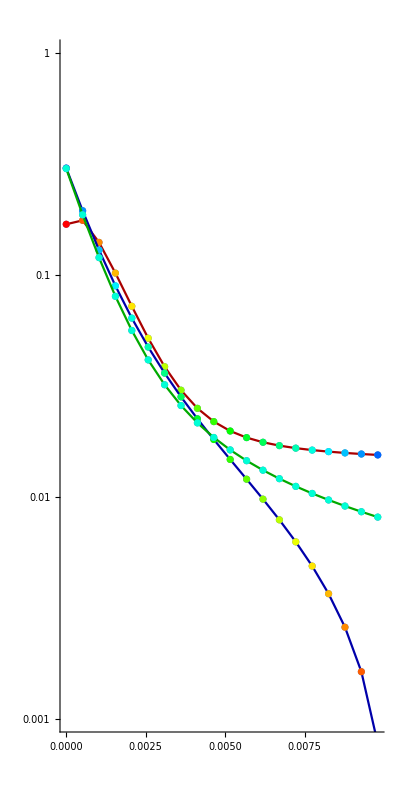

```mathematica
Show[plot1JoinedEarly,plot1DotsEarly,plot2JoinedEarly,plot2DotsEarly,plot3JoinedEarly,plot3DotsEarly,PlotRange->Log[{0.001, 1}],AspectRatio->2]
```

## Look at multiple spacer dynamics

```mathematica
ηRules={η[1]->0.001, η[2]->0.002,η[3]->0.003,η[4]->0.004,η[5]->0.005,η[6]->0.006,η[7]->0.007,η[8]->0.008,η[9]->0.009,η[10]->0.20};
sampleRulesMulti=Join[{nsp->10,f[_]->2,b->100,μ->1,k->0.01,η[0]->1,g->0.05,α[_]->0.01,Kpop->10^2,tmax->4096},ηRules];
nInitialRules={n[1][0]==0.06,n[2][0]==0.07,n[3][0]==0.06,n[4][0]==0.05,n[5][0]==0.04,n[6][0]==0.10,n[7][0]==0.03,n[8][0]==0.08,n[9][0]==0.06,n[10][0]==0.05};
sampleICMulti=Join[{n[0][0]==10^0,v[0]==10^1},nInitialRules,Table[nI[i][0]==0,{i, 0,(nsp/.sampleRulesMulti)}]];
```

```mathematica
eqns=createEquations[sampleRulesMulti]~Join~sampleICMulti;
```

```mathematica
soln=NDSolve[eqns,Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.sampleRulesMulti)}]]~Join~{v}],{t,0,(tmax/.sampleRulesMulti)}];
```

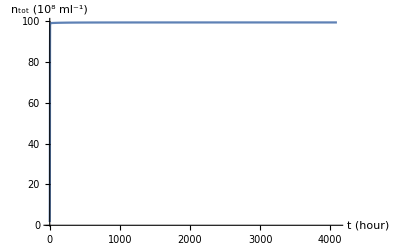

```mathematica
Plot[Evaluate[Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRulesMulti)}]]/.soln,{t,0,(tmax/.sampleRulesMulti)},PlotRange->All,AxesLabel->{"t (hour)", "n_tot (10^8 ml^-1)"}]
```

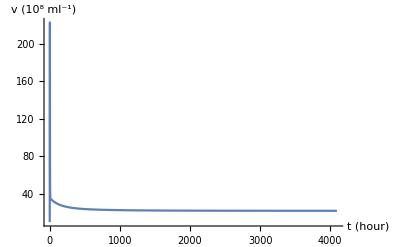

```mathematica
Plot[v[t]/.soln,{t,0,(tmax/.sampleRulesMulti)},AxesLabel->{"t (hour)", "v (10^8 ml^-1)"},PlotRange->All]
```

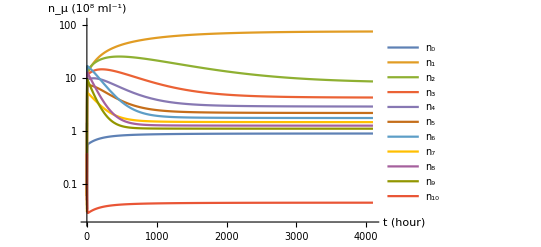

```mathematica
LogPlot[Evaluate[Table[n[i][t],{i,0,(nsp/.sampleRulesMulti)}]/.soln],{t,0,(tmax/.sampleRulesMulti)},PlotRange->All,AxesLabel->{"t (hour)", "n_μ (10^8 ml^-1)"},PlotLegends->Table[Subscript[n, i],{i,0,(nsp/.sampleRulesMulti)}]]
```

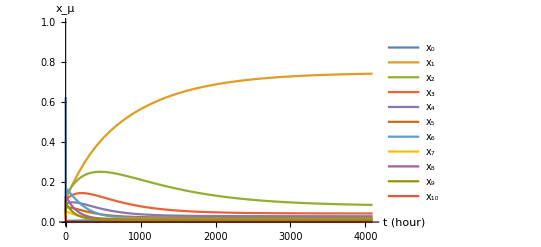

```mathematica
Plot[Evaluate[Table[n[i][t],{i,0,(nsp/.sampleRulesMulti)}]/Sum[n[k][t]+nI[k][t],{k,0,(nsp/.sampleRulesMulti)}]/.soln],{t,0,(tmax/.sampleRulesMulti)},PlotRange->{0,1},AxesLabel->{"t (hour)", "x_μ"},PlotLegends->Table[Subscript[x, i],{i,0,(nsp/.sampleRulesMulti)}]]
```

## Check analytical calculations for single protospacer problem

Defining the equations

```mathematica
eqns0={
n0'[t]==f0(1-n[t]/Kpop)n0[t]+k n1[t]-g v[t] n0[t],
I0'[t]==g v[t] n0[t]-μ I0[t],
n1'[t]==f1(1-n[t]/Kpop)n1[t]-k n1[t]-g η v[t]n1[t]+α μ I0[t],
I1'[t]==g η v[t]n1[t]-μ I1[t],
v'[t]==b(1-α)μ I0[t]+ b μ I1[t]- g v[t](n0[t]+n1[t])
};
```

```mathematica
nTotRule={n->(n0[#]+I0[#]+n1[#]+I1[#]&)};
aRule={α->1-a};
eqns=eqns0/.aRule;
```

```mathematica
eqnsRules=eqns/.(A_==B_)->(A->B)
```

{n0'[t]→f0 (1-n[t]/Kpop) n0[t]+k n1[t]-g n0[t] v[t],I0'[t]→-μ I0[t]+g n0[t] v[t],n1'[t]→(1-a) μ I0[t]-k n1[t]+f1 (1-n[t]/Kpop) n1[t]-g η n1[t] v[t],I1'[t]→-μ I1[t]+g η n1[t] v[t],v'[t]→a b μ I0[t]+b μ I1[t]-g (n0[t]+n1[t]) v[t]}

Compare to result from createEquations

```mathematica
eqnsAgain=createEquations[{nsp->1,η[0]->1,η[1]->η}]/.n[0]->n0/.nI[0]->I0/.n[1]->n1/.nI[1]->I1/.f[0]->f0/.f[1]->f1/.α[1]->α;
```

```mathematica
ShouldBeTrue=eqnsAgain/.(eqnsRules/.nTotRule)/.aRule//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqns/.nTotRule/.(eqnsAgain/.(A_==B_)->(A->B))/.aRule//Simplify
```

{True,True,True,True,True}

Checking differential equation for n(t)

This is our analytical result for n'(t):

```mathematica
ourNOde=(f0 n0[t]+f1 n1[t])(1-n[t]/Kpop)-μ a I0[t]-μ I1[t];
```

```mathematica
ShouldBeZero=(n0'[t]+I0'[t]+n1'[t]+I1'[t]/.eqnsRules)-ourNOde//Simplify
```

0

Checking the steady-state analytical results

```mathematica
eqnsSteady=eqns/.f_'->(0&)/.f_[t]->f
```

{0==f0 (1-n/Kpop) n0+k n1-g n0 v,0==g n0 v-I0 μ,0==-k n1+f1 (1-n/Kpop) n1-g n1 v η+(1-a) I0 μ,0==g n1 v η-I1 μ,0==-g (n0+n1) v+a b I0 μ+b I1 μ}

```mathematica
calFRule={n->Kpop(1-calF)};
```

Here are some expressions we get analytically.

```mathematica
vRule1={v->1/g(f0 calF+k (b a - 1)/(1-b η))};
```

```mathematica
n0Rule1={n0->(μ(1-b η))/(b μ(a-η)+(f0 calF + k (b a - 1)/(1-b η))(1-η-η b (1-a)))n};
n0Rule2={n0->(1-b η)/(b(a-η)+(g v)/μ(1-η-η b(1-a)))n};
n1Rule1={n1->(b a - 1)/(1-b η)n0};
```

```mathematica
I0Rule={I0->(g v n0)/μ};
I1Rule={I1->(g η v n1)/μ};
```

```mathematica
calFRule1={calF->k/f0 1/(1-b η)(b a - 1)/(b-1+(f1/f0-1)(b a-1)/(a-η))};
calFRule2={calF->k/f0(a-η)/(1-b η)(b a - 1)/(1-a-η(b-1)+f1/f0(b a-1))};
```

```mathematica
ShouldBeTrue=eqnsSteady/.I0Rule/.I1Rule/.n1Rule1/.n0Rule1/.calFRule/.vRule1/.calFRule1//Simplify//Expand//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsSteady/.I0Rule/.I1Rule/.n1Rule1/.n0Rule1/.calFRule/.vRule1/.calFRule2//Simplify//Expand//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsSteady/.I0Rule/.I1Rule/.n1Rule1/.n0Rule2/.calFRule/.vRule1/.calFRule1//Simplify//Expand//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeZero=(n0/.n0Rule1)-(n0/.n0Rule2/.vRule1)//Simplify
```

0

Critical value of η

```mathematica
ηcEquation=Collect[Assuming[a≠η,k(b a - 1)/(b f0 (b-1))((a-η)/calF-(a-η)/.calFRule1/.f1->(1+ϵ) f0//Simplify)],η,Collect[Simplify[#],ϵ,Simplify]&]
```

(a ((-1+b) f0+k-a b k))/((-1+b) b f0)+((-1+a b) ϵ)/((-1+b) b)+((-(-1+b) (1+a b) f0+(-1+a b) k)/((-1+b) b f0)+((1-a b) ϵ)/(-1+b)) η+η^2

```mathematica
ηcRootRules=Assuming[a>η&&a>1/b&&η<1/b&&a>0&&b>1&&f0>0&&k>0,Solve[ηcEquation==0,η]//Simplify]
```

{{η→1/(2 (-1+b) b f0)(f0 (-1+a b^2 (1+ϵ)-b (-1+a+ϵ))-(-1+a b) (k+√(k^2-2 f0 k (1+b (-1+ϵ))+f0^2 (-1+b+b ϵ)^2)))},{η→1/(2 (-1+b) b f0)(f0 (-1+a b^2 (1+ϵ)-b (-1+a+ϵ))+(-1+a b) (-k+√(k^2-2 f0 k (1+b (-1+ϵ))+f0^2 (-1+b+b ϵ)^2)))}}

```mathematica
ηcExpansion=Assuming[b>1&&f0>0&&k>0,Series[η/.ηcRootRules,{ϵ,0,4}]//Simplify];
```

The second solution can be ignored since it is η_c>a, which is unlikely to be true in any realistic conditions.

```mathematica
ηcExpansionPaper={ηc->1/b(1-k/f0(b a - 1)/(b-1))+ϵ (k (b a - 1))/f0 1/((b-1)(b-1+k/f0))-ϵ^2(k (b a - 1))/f0 b/(b-1+k/f0)^3+ϵ^3(k (b a - 1))/f0(b^2(b-1-k/f0))/(b-1+k/f0)^5-ϵ^4(k (b a - 1))/f0(b^3((b-1)^2-3(b-1)k/f0+(k/f0)^2))/(b-1+k/f0)^7};
```

```mathematica
shouldBeZero=(ηc/.ηcExpansionPaper)-Normal[ηcExpansion[[1]]]//Simplify
```

0

```mathematica
ηcExpansionAlt={ηc->1/b-k/f0(b a - 1)/(b (b-1))(1-ϵ b 1/(b-1+k/f0)+(ϵ b)^2(b-1)/(b-1+k/f0)^3-(ϵ b)^3((b-1)(b-1-k/f0))/(b-1+k/f0)^5+(ϵ b)^4((b-1)((b-1)^2-3(b-1)k/f0+(k/f0)^2))/(b-1+k/f0)^7)};
```

```mathematica
shouldBeZero=(ηc/.ηcExpansionAlt)-Normal[ηcExpansion[[1]]]//Simplify
```

0

What happens when b>>1? Let’s write everything in terms of the product η b.

```mathematica
ηbEquation=Collect[b^2 ηcEquation/.η->ηb/b,ηb,Collect[Simplify[#],ϵ,Simplify]&]
```

(a b ((-1+b) f0+k-a b k))/((-1+b) f0)+(b (-1+a b) ϵ)/(-1+b)+((-(-1+b) (1+a b) f0+(-1+a b) k)/((-1+b) f0)+((b-a b^2) ϵ)/(-1+b)) ηb+ηb^2

```mathematica
ηbSolnLargeB=ηb/.Solve[Normal[Series[ηbEquation,{b,Infinity,-1}]//Simplify]==0,ηb][[1]]//Simplify
```

(f0-a k+f0 ϵ)/(f0+f0 ϵ)

```mathematica
ShouldBeZero=ηbSolnLargeB-(1-k/f0 a/(1+ϵ))//Simplify
```

0

```mathematica
ηbEquationNoR=Series[((a-η)/calF-(a-η)/.calFRule1/.η->ηb/b//Simplify),{b,Infinity,0}]
```

(f1-a k-f1 ηb)/k+O[1/b]^1

```mathematica
ηbSolnLargeBNoR=ηb/.Solve[Normal[ηbEquationNoR]==0,ηb][[1]];
```

```mathematica
ShouldBeZero=ηbSolnLargeBNoR-(1-(k a)/f1)//Simplify
```

0

```mathematica
Assuming[f0>0&&ϵ>-1,(Series[b η/.ηcRootRules[[1]],{b,Infinity,1}]//Simplify)/.ϵ->f1/f0-1//Simplify]
```

(1-(a k)/f1)+(k (f1^2-a (f0 (f1-k)+f1 k)))/(f1^3 b)+O[1/b]^2

Rederiving analytical solution

```mathematica
rederiveIEqns=Solve[eqnsSteady[[{2,4}]],{I0,I1}][[1]]
```

{I0→(g n0 v)/μ,I1→(g n1 v η)/μ}

```mathematica
rederiveN1Rule1=Solve[eqnsSteady[[1]]/.calFRule,n1][[1]]//Simplify
```

{n1→(-calF f0 n0+g n0 v)/k}

```mathematica
rederiveVRule=Solve[Assuming[v≠0&&n0≠0,eqnsSteady[[5]]/.rederiveIEqns/.rederiveN1Rule1//Simplify],v][[1]]//Simplify
```

{v→(calF f0-k+a b k-b calF f0 η)/(g-b g η)}

```mathematica
rederiveN1Rule2=(rederiveN1Rule1/.rederiveVRule)//Simplify
```

{n1→(n0-a b n0)/(-1+b η)}

```mathematica
rederiveCalFRule=Solve[Assuming[n0≠0,eqnsSteady[[3]]/.calFRule/.rederiveIEqns/.rederiveN1Rule1/.rederiveVRule//Simplify],calF][[1]]
```

{calF→((-1+a b) k (a-η))/((-1+b η) (-f0+a f0+f1-a b f1-f0 η+b f0 η))}

```mathematica
rederiveN0Rule=Solve[(1-(n0+I0+n1+I1)/Kpop==calF/.rederiveIEqns/.rederiveN1Rule1)//Simplify,n0][[1]]/.rederiveVRule//Simplify
```

{n0→((-1+calF) Kpop (-1+b η)^2 μ)/(-(-1+a b) k (1+(-1+(-1+a) b) η)+calF f0 (-1+b η) (1+(-1+(-1+a) b) η)+b (a-η) (-1+b η) μ)}

Checking matching between rederived solution and the one we had

```mathematica
ShouldBeZero=(I0/.rederiveIEqns)-(I0/.I0Rule)//Simplify
```

0

```mathematica
ShouldBeZero=(I1/.rederiveIEqns)-(I1/.I1Rule)//Simplify
```

0

```mathematica
ShouldBeZero=(calF/.calFRule1)-(calF/.rederiveCalFRule)//Simplify
```

0

```mathematica
ShouldBeZero=(v/.rederiveVRule)-(v/.vRule1)//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.n1Rule1)-(n1/.rederiveN1Rule2)//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.n1Rule1)-(n1/.rederiveN1Rule1/.vRule1)//Simplify
```

0

```mathematica
ShouldBeZero=(n0/.rederiveN0Rule)-(n0/.n0Rule1/.calFRule)//Simplify
```

0

When there is no spacer loss

```mathematica
ShouldBeZero=(n0/n/.n0Rule1/.calFRule/.calFRule1/.k->0)-(1-b η)/(b(a-η))//Simplify
```

0

```mathematica
ShouldBeZero=(n1/n/.n1Rule1/.n0Rule1/.calFRule/.calFRule1/.k->0)-(b a - 1)/(b(a-η))//Simplify
```

0

```mathematica
ShouldBeZero=v/.vRule1/.calFRule1/.k->0//Simplify
```

0

When there is no self-targeting, f_1=f_0

```mathematica
ShouldBeZero=(calF/.calFRule1/.f1->f0)-k/f0 1/(1-b η)(b a-1)/(b-1)//Simplify
```

0

```mathematica
ShouldBeZero=(g v/.vRule1)-calF b f0/.calFRule1/.f1->f0//Simplify
```

0

```mathematica
ShouldBeZero=((n0/n/.n0Rule1/.calFRule)-(μ/b(1-b η)/(μ(a-η)+f0 calF(1-η-η b(1-a)))))/.calFRule1/.f1->f0//Simplify
```

0

```mathematica
ShouldBeZero=((n1/n/.n1Rule1/.n0Rule1/.calFRule)-(μ/b(b a-1)/(μ(a-η)+f0 calF(1-η-η b(1-a)))))/.calFRule1/.f1->f0//Simplify
```

0

Check n_i+I_i steady state

```mathematica
ShouldBeZero=(n0+I0/.I0Rule/.n0Rule2)-((1-b η)/(b(a-η)-(g v)/(g v + μ)(1-η)(b a-1))n)//Simplify
```

0

```mathematica
ShouldBeZero=(n1+I1/.I1Rule/.n1Rule1/.n0Rule2)-((b a-1)/(b(a-η)+(g v)/(η g v + μ)(1-η)(1-b η))n)//Simplify
```

0

## Check analytical calculations for multiple spacer case

Steady state

```mathematica
testAnalyticalSolution[ns_]:=
Module[{eqns=createEquations[{nsp->ns,η[0]->1}]/.A_'[t]->0/.A_[t]->A,
n0Rule1,nIRules,η1ηbarRule,f1fbarRule,n1nsumRule,α1aRule,vRule1,calFRule1,calFRule2,n0Rule2,calFRule3,n0Rule3,nsumRule,otherNRules},
n0Rule1=Solve[eqns[[1]]/.nI[0]->Kpop(1-calF)-n[0]-Sum[n[i]+nI[i],{i,1,ns}],n[0]][[1]];
nIRules=Prepend[Table[Solve[eqns[[ns+3+i]],nI[i]][[1]][[1]],{i,1,ns}],
Solve[eqns[[2]],nI[0]][[1]][[1]]];
η1ηbarRule={η[1]->1/n[1](ηbar Sum[n[i],{i,1,ns}]-Sum[η[j]n[j],{j,2,ns}])};
f1fbarRule={f[1]->1/n[1](fbar Sum[n[i],{i,1,ns}]-Sum[f[j]n[j],{j,2,ns}])};
n1nsumRule={n[1]->nsum-Sum[n[j],{j,2,ns}]};
α1aRule={α[1]->1-a-Sum[α[j],{j,2,ns}]};
vRule1=Solve[Assuming[nsum≠0&&g≠0&&v≠0,eqns[[3]]/.nIRules/.n0Rule1/.η1ηbarRule/.n1nsumRule/.α1aRule//Simplify],v][[1]]//Simplify;
n0Rule2=Simplify[n0Rule1/.vRule1/.n1nsumRule];
calFRule1={Kpop->Sum[n[ν]+nI[ν],{ν,0,ns}]/(1-calF)};
calFRule2=Solve[Assuming[fbar≠0&&nsum≠0&&μ≠0&&Kpop≠0,0==(Plus@@(eqns[[4;;3+ns]]/.(0==B_)->B))/.calFRule1/.nIRules/.η1ηbarRule/.
f1fbarRule/.n1nsumRule/.α1aRule/.n0Rule2/.vRule1//Simplify],calF][[1]]//Simplify;
calFRule3=Solve[v==(v/.vRule1),calF][[1]]//Simplify;
nsumRule=Solve[n[0]==(n[0]/.n0Rule2),nsum][[1]];
n0Rule3=Solve[((n[0]+nI[0]+Sum[n[i]+nI[i],{i,1,ns}]==ntot)/.nIRules/.η1ηbarRule/.n1nsumRule/.α1aRule/.nsumRule/.calFRule3//Simplify),n[0]][[1]]//Simplify;
otherNRules=Table[Solve[eqns[[3+i]]/.calFRule1/.nIRules,n[i]][[1]][[1]],{i,1,ns}];
{(n[0]/.n0Rule1)-k/(g v-f[0] calF)Sum[n[i],{i,1,ns}],
(nI[0]/.nIRules)-(g v n[0])/μ}~Join~
Table[(nI[i]/.nIRules)-(η[i] g v n[i])/μ,{i,1,ns}]~Join~{
Simplify[(g v/.vRule1)-f[0] calF-k (a b-1)/(1-b ηbar)],
Simplify[(n[0]/.n0Rule1/.vRule1)-(1-b ηbar)/(a b-1)Sum[n[i],{i,1,ns}]],
Simplify[(calF/.calFRule2)-(k/f[0] (b a-1)/(1-b ηbar)1/((b-1)+(fbar/f[0]-1)(b a-1)/(a-ηbar)))],
Simplify[(n[0]/.n0Rule3)-(1-b ηbar)/(b(a-ηbar)+g v (1-ηbar-ηbar b(1-a))/μ)ntot]
}~Join~Table[
(n[i]/.otherNRules)-(α[i] g v)/(k + η[i] g v-f[i]calF)n[0],{i,1,ns}]~Join~Table[
Simplify[(n[i]/.otherNRules/.vRule1)-α[i](k (b a-1)/(1-b ηbar)+f[0]calF)/(k (1+η[i] (b a-1)/(1-b ηbar))-f[0]calF(f[i]/f[0]-η[i]))n[0]],{i,1,ns}]];
```

```mathematica
ShouldBeZero=testAnalyticalSolution[1]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[2]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[3]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[6]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[7]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[8]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[9]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShouldBeZero=testAnalyticalSolution[10]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Equation for n_total

```mathematica
testAnalyticalNtotal[ns_]:=Module[{eqnsRules=createEquations[{nsp->ns,η[0]->1}]/.(A_==B_)->(A->B),ntotRule,f1fbarRule,n1nsumRule,nI1nIsumRule,α1aRule},
ntotRule={Kpop->Kpop Sum[n[ν][t]+nI[ν][t],{ν,0,ns}]/ntot[t]};
f1fbarRule={f[1]->1/(n[1][t])(fbar Sum[n[i][t],{i,1,ns}]-Sum[f[j]n[j][t],{j,2,ns}])};
n1nsumRule={n[1][t]->nsum[t]-Sum[n[j][t],{j,2,ns}]};
nI1nIsumRule={nI[1][t]->nIsum[t]-Sum[nI[j][t],{j,2,ns}]};
α1aRule={α[1]->1-a-Sum[α[j],{j,2,ns}]};
(Sum[n[ν]'[t]+nI[ν]'[t],{ν,0,ns}]/.eqnsRules/.ntotRule/.f1fbarRule/.n1nsumRule/.nI1nIsumRule/.α1aRule//Simplify)-((1-ntot[t]/Kpop)(f[0]n[0][t]+fbar nsum[t])-μ a nI[0][t]-μ nIsum[t])//Simplify
];
```

```mathematica
ShouldBeZero=Table[testAnalyticalNtotal[n],{n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

## Check analytical calculations for serial dilution case

Doing this only for the case of a single protospacer.

Defining the equations

```mathematica
eqnsDilution={
n0'[t]==(f0(1-n[t]/Kpop)-sb)n0[t]+k n1[t]-g n0[t] v[t],
n1'[t]==(f1(1-n[t]/Kpop)-sb)n1[t]-k n1[t]-g η n1[t] v[t] + α μ I0[t],
I0'[t]==g n0[t] v[t]-μ I0[t]-sb I0[t],
I1'[t]==g η n1[t] v[t] - μ I1[t] - sb I1[t],
v'[t]==b(μ (1-α) I0[t]+μ I1[t])-g v[t](n0[t]+n1[t])-sv v[t]
};
```

```mathematica
nTotRule={n->(n0[#]+I0[#]+n1[#]+I1[#]&)};
```

```mathematica
eqnsDilutionRules=eqnsDilution/.(A_==B_)->(A->B);
```

Comparing to result from createEquationsGeneral

```mathematica
eqnsDilution0 = createEquationsGeneral[{nsp->1, η[0]->1,η[1]->η}]/.n[0]->n0/.nI[0]->I0/.n[1]->n1/.nI[1]->I1/.f[0]->f0/.f[1]->f1/.α[1]->α/.s[_]->sb;
```

```mathematica
ShouldBeTrue=eqnsDilution0/.(eqnsDilutionRules/.nTotRule)//Simplify
```

createEquationsGeneral[{nsp→1,η[0]→1,η[1]→η}]

```mathematica
ShouldBeTrue=eqnsDilution/.nTotRule/.(eqnsDilution0/.(A_==B_)->(A->B))//Simplify
```

ReplaceAll::reps: {createEquationsGeneral[{nsp→1,η[0]→1,η[1]→η}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{g n0[t] v[t]+n0'[t]==k n1[t]+n0[t] (-sb+f0 (1-(I0[t]+I1[t]+n0[t]+n1[t])/Kpop)),n1[t] (k+g η v[t])+n1'[t]==α μ I0[t]+n1[t] (-sb+f1 (1-(I0[t]+I1[t]+n0[t]+n1[t])/Kpop)),(sb+μ) I0[t]+I0'[t]==g n0[t] v[t],(sb+μ) I1[t]+I1'[t]==g η n1[t] v[t],b (-1+α) μ I0[t]+(sv+g n0[t]+g n1[t]) v[t]+v'[t]==b μ I1[t]}/.createEquationsGeneral[{nsp→1,η[0]→1,η[1]→η}]

Checking differential equation for n(t)

This is our analytical result for n'(t):

```mathematica
ourNOdeDilution=(f0 n0[t]+f1 n1[t])(1-n[t]/Kpop)-μ (1-α) I0[t]-μ I1[t]-sb n[t];
```

```mathematica
ShouldBeZero=(n0'[t]+I0'[t]+n1'[t]+I1'[t]/.eqnsDilutionRules)-ourNOdeDilution/.nTotRule//Simplify
```

0

Checking the steady-state analytical results

```mathematica
eqnsDilutionSteady=eqnsDilution/.f_'->(0&)/.f_[t]->f
```

{0==k n1+n0 (f0 (1-n/Kpop)-sb)-g n0 v,0==-k n1+n1 (f1 (1-n/Kpop)-sb)-g n1 v η+I0 α μ,0==-I0 sb+g n0 v-I0 μ,0==-I1 sb+g n1 v η-I1 μ,0==-g (n0+n1) v-sv v+b (I1 μ+I0 (1-α) μ)}

```mathematica
calFRule={n->Kpop(1-calF)};
```

```mathematica
nTotRuleSteady={n->(n0+n1+I0+I1)};
```

### When v=0

```mathematica
noVRule={v->0};
```

Here are some expressions we get analytically.

```mathematica
solnNoV1={n0->0,n1->0,I0->0,I1->0};
```

```mathematica
solnNoV2={n1->0,n0->Kpop(1-sb/f0),I0->0,I1->0};
solnNoV3={n0->Kpop (1-(sb + k)/f1)/(1+sb/k(1-f0/f1)-f0/f1),n1->Kpop ((1-(sb + k)/f1)(sb/k(1-f0/f1)-f0/f1))/(1+sb/k(1-f0/f1)-f0/f1),I0->0,I1->0};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.noVRule/.solnNoV1//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.noVRule/.nTotRuleSteady/.solnNoV2//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.noVRule/.nTotRuleSteady/.solnNoV3//Simplify
```

{True,True,True,True,True}

### When v≠0, n_0=0

This requires k=0 (otherwise n_1 and v must also be zero).

```mathematica
vRuleNoN0={v->(f1(1-n1/Kpop)-sb)/(g η(1+f1/(μ+sb)n1/Kpop))};
```

```mathematica
n1RuleNoN0={n1->sv/g 1/(b η w-1)};
```

```mathematica
wRule={w->μ/(μ+sb)};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteady/.nTotRuleSteady/.{n0->0,I0->0,k->0}/.I1->(g η v)/(μ+sb)n1/.vRuleNoN0/.n1RuleNoN0/.wRule//Simplify
```

{True,True,True,True,True}

```mathematica
ShouldBeZero=(v/.vRuleNoN0/.n1RuleNoN0/.wRule/.sb->0)-(f1 μ (g Kpop(b η-1)-sv))/(g η(μ g Kpop(b η-1)+f1 sv))//Simplify
```

0

### When v≠0,n_0≠0,n_1≠0

```mathematica
IRulesDilution={I0->(g v)/(μ+sb)n0,I1->(g η v)/(μ+sb)n1};
```

```mathematica
vRuleDilution1={v->((f0 n0 + f1 n1 + sb Kpop)calF-sb Kpop)/(g w ((1-α)n0+η n1))};
nRuleDilution1={n1->((b w(1-α)-1)n0-sv/g)/(1-b η w)};
```

```mathematica
vRuleDilution2={v->((f0 n0 + f1 n1)(1-(n0+n1)/Kpop)-sb(n0+n1))/(g w ((1-α)n0+η n1+(f0 n0 + f1 n1 + sb Kpop)/μ(n0+η n1)/Kpop))};
```

```mathematica
vRuleDilution3={v->(f0(1-(n0+n1)/Kpop)-sb+k n1/n0)/(g(1+f0/(μ+sb)(n0+η n1)/Kpop))};
```

```mathematica
wRule={w->μ/(μ+sb)};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteady[[3;;5]]/.IRulesDilution/.calFRule/.vRuleDilution1/.nRuleDilution1/.wRule//Simplify
```

{True,True,True}

```mathematica
ShouldBeZero=(Collect[Sum[eqnsDilutionSteady[[i]]/.(A_==B_)->B,{i,1,4}],sb,Simplify]/.-n0-n1-I0-I1->-n/.calFRule//Simplify)/.IRulesDilution/.vRuleDilution1/.w->μ/(μ+sb)//Simplify
```

0

Test a different expression for the viral population.

```mathematica
ShouldBeZero=Collect[((Sum[eqnsDilutionSteady[[i]]/.(A_==B_)->(A-B),{i,1,4}]/.n->n0+n1+I0+I1//Simplify)/.IRulesDilution//Simplify),v,Simplify]/.vRuleDilution2/.wRule//Simplify
```

0

```mathematica
ShouldBeTrue=eqnsDilutionSteady[[3;;5]]/.IRulesDilution/.calFRule/.vRuleDilution2/.nRuleDilution1/.wRule//Simplify
```

{True,True,True}

And a third expression for the viral population.

```mathematica
ShouldBeTrue=eqnsDilutionSteady[[{1,3,4,5}]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilution3/.nRuleDilution1/.wRule//Simplify
```

{True,True,True,True}

This leaves only one equation to be satisfied -- the one that sets the value of n_0 (or, equivalently, calF).

```mathematica
(*Solve[((eqnsDilutionSteady[[1]]/.(A_==B_)->(A-B))/.n->(n0+n1+I0+I1)/.IRulesDilution/.vRuleDilution2/.nRuleDilution1/.wRule//Simplify)==0,n0]*)
```

```mathematica
(*Solve[((eqnsDilutionSteady[[2]]/.(A_==B_)->(A-B))/.n->(n0+n1+I0+I1)/.IRulesDilution/.vRuleDilution3/.nRuleDilution1/.wRule//Simplify)==0,n0]*)
```

Looks like full solution is not worth it...

### When k=0

Assuming still that v≠0,n_0≠0,n_1≠0.

```mathematica
eqnsDilutionSteadyNoLoss=eqnsDilutionSteady/.k->0;
```

```mathematica
IRulesDilution={I0->(g v)/(μ+sb)n0,I1->(g η v)/(μ+sb)n1};
```

```mathematica
vRuleDilutionNoLoss1={v->(f0 calF-sb)/g};
nRuleDilution1={n1->((b w(1-α)-1)n0-sv/g)/(1-b η w)};
```

```mathematica
wRule={w->μ/(μ+sb)};
```

```mathematica
vRuleDilutionNoLoss2={v->(f0 (1-(n0+n1)/Kpop)-sb)/(g(1+f0/(μ+sb)(n0+η n1)/Kpop))};
```

```mathematica
ShouldBeTrue=eqnsDilutionSteadyNoLoss[[{1,3,4,5}]]/.IRulesDilution/.calFRule/.vRuleDilutionNoLoss1/.nRuleDilution1/.wRule//Simplify
```

{True,True,True,True}

```mathematica
ShouldBeZero=(eqnsDilutionSteadyNoLoss[[1]]/.(A_==B_)->(A-B)/.n->n0+n1+I0+I1//Simplify)/.IRulesDilution/.vRuleDilutionNoLoss2//Simplify
```

0

```mathematica
ShouldBeTrue=eqnsDilutionSteadyNoLoss[[{1,3,4,5}]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.wRule//Simplify
```

{True,True,True,True}

One equation left, but I guess this also looks too messy...

```mathematica
(*Solve[(eqnsDilutionSteadyNoLoss[[2]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.wRule//Simplify),n0]//Simplify*)
```

### When k=0 and f_1≈f_0

#### Derive solution

Do a standard expansion of n_0 in γ=(f_1-f_0)/f_0.

```mathematica
γRule={f1->f0(1+γ)};
n0SeriesRule={n0->n0s0+γ n0s1};
```

Plug the series expansion into the remaining equation, and keep only the terms for γ^0 and γ^1.

```mathematica
lastEquationDilutionNoLossAlmostEqualGrowth=CoefficientList[Normal[Series[((eqnsDilutionSteadyNoLoss[[2]]/.(A_==B_)->(A-B)/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.wRule/.γRule//Simplify)/.n0SeriesRule//Simplify),{γ,0,1}]//Simplify],γ]
```

{-(((sv (-1+η) (sb+μ)^2+g n0s0 (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)) (-g Kpop sb (sb+μ-b η μ)+f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g (sb+μ-b η μ) (g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ))))),1/(sb+μ-b η μ)n0s1 η (sb+μ) ((b f0 (-1+α+η) μ (sv (sb+μ)+g n0s0 (sb+μ-b μ+b α μ)))/(-g Kpop (sb+μ) (sb+μ-b η μ)+f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))+((sb+μ) (sb+μ-b η μ) (-f0 sv+g Kpop (sb+μ-b μ+b α μ)) (g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))^2)+1/(g (sb+μ-b η μ))((f0 (sv (sb+μ)+g n0s0 (sb+μ-b μ+b α μ)) (sv (sb (-1+η)-μ) (sb+μ)-g (b n0s1 (-1+α+η) μ (sb+μ)+Kpop (sb+μ) (sb+μ-b η μ)+n0s0 (-sb^2 (-1+η)-sb (1+b (-1+α)) (-1+η) μ+b (-1+α+η) μ^2))))/(-g Kpop (sb+μ) (sb+μ-b η μ)+f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))-(g n0s1 (sb+μ)^2 (sb+μ-b η μ) (-f0 sv+g Kpop (sb+μ-b μ+b α μ)) (g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))^2)+α μ ((b f0 g n0s0 n0s1 (-1+α+η) μ)/(-g Kpop (sb+μ) (sb+μ-b η μ)+f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))+(n0s1 (sb+μ) (-f0 sv η+g Kpop (sb+μ-b η μ)) (g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g (b n0s0 (-1+α+η) μ+Kpop (sb+μ-b η μ)))))/(g Kpop (sb+μ) (sb+μ-b η μ)-f0 (sv η (sb+μ)+g n0s0 (sb (-1+η)+(-1+η+b α η) μ)))^2)}

Can use coefficient for γ^0 to find the zeroth-order solutions.

```mathematica
n0s0DilutionNoLossAlmostEqualGrowth=Solve[lastEquationDilutionNoLossAlmostEqualGrowth[[1]]==0,n0s0]//Simplify
```

{{n0s0→(g Kpop sb (sb+μ-b η μ)-f0 (sv (sb+μ)+g Kpop (sb+μ-b η μ)))/(b f0 g (-1+α+η) μ)},{n0s0→-(sv (-1+η) (sb+μ)^2)/(g (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2))}}

Now use the coefficient for γ^1 to find the first order corrections.

```mathematica
n0s1DilutionNoLossAlmostEqualGrowth1=Solve[(lastEquationDilutionNoLossAlmostEqualGrowth[[2]]/.n0s0DilutionNoLossAlmostEqualGrowth[[1]])==0,n0s1][[1]]//Simplify
```

{n0s1→-((sb (-sb+(-1+b η) μ) (-g Kpop sb (sb+μ-b μ+b α μ)+f0 (sv (sb+μ)+g Kpop (sb+μ-b μ+b α μ))) (g Kpop (-sb^2 (-1+η)-sb (1+b (-1+α)) (-1+η) μ+b (-1+α+η) μ^2)+f0 (sv (-1+η) (sb+μ)+g Kpop (sb (-1+η)+(-1+η+b α η) μ))))/(b^2 f0 g (-1+α+η)^2 μ^2 (g Kpop sb (-sb^2 (-1+η)-sb (-2+α+b (-1+α) (-1+η)+2 η) μ+(-1+b) (-1+α+η) μ^2)+f0 (sv (sb+μ) (sb (-1+η)+(-1+α+η) μ)+g Kpop (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)))))}

```mathematica
n0s1DilutionNoLossAlmostEqualGrowth2=Solve[(lastEquationDilutionNoLossAlmostEqualGrowth[[2]]/.n0s0DilutionNoLossAlmostEqualGrowth[[2]])==0,n0s1][[1]]//Simplify
```

{n0s1→-((f0 sv α μ (sb+μ)^2 (sb+μ-b η μ) (sv μ (sb (-1+α+η-α η)+(-1+α+η) μ)+g Kpop (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)))/(g (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)^2 (g Kpop sb (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)-f0 (sv (sb+μ) (sb (-1+η)+(-1+α+η) μ)+g Kpop (sb^2 (-1+η)+sb (-2+α+b (-1+α) (-1+η)+2 η) μ-(-1+b) (-1+α+η) μ^2)))))}

#### Check results from paper for s_b=0.

```mathematica
n0s0/.n0s0DilutionNoLossAlmostEqualGrowth/.wRule/.sb->0//Simplify
```

{(-sv+g Kpop (-1+b η))/(b g (-1+α+η)),(sv (-1+η))/((-1+b) g (-1+α+η))}

First solution corresponds to no virus -- it should have been treated above, but it doesn’t seem to have been...

This is an exact solution, not just an expansion in γ.

```mathematica
ShouldBeZero=v/.vRuleDilutionNoLoss2/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0//Simplify
```

0

```mathematica
ShouldBeTrue=eqnsDilutionSteadyNoLoss[[2]]/.n->n0+n1+I0+I1/.IRulesDilution/.vRuleDilutionNoLoss2/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0//Simplify
```

True

```mathematica
ShouldBeZero=(n0+n1-Kpop)/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[1]]/.wRule/.sb->0)-((Kpop (b(1-α)-1))/(b(1-α-η))-sv/(b g(1-α-η)))//Simplify
```

0

Second solution.

```mathematica
ShouldBeZero={(n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[2]]/.wRule/.sb->0)-(sv(1-η))/(g(b-1)(1-α-η)),
(n0s1/.n0s1DilutionNoLossAlmostEqualGrowth2/.wRule/.sb->0)-(sv α (1-b η))/(g(b-1)^2(1-α-η)^2)}//Simplify
```

{0,0}

Note that we’re treating the virus only at zeroth order here.

```mathematica
ShouldBeZero=(v/.vRuleDilutionNoLoss2/.nRuleDilution1/.n0->n0s0/.n0s0DilutionNoLossAlmostEqualGrowth[[2]]/.wRule/.sb->0)-(f0 μ(1-α-η)((b-1)g Kpop - sv))/(g((b-1)μ g Kpop(1-α-η)+f0 sv (1-α η-η)))//Simplify
```

0

```mathematica
ShouldBeZero=((CoefficientList[Normal[Series[(n1/.nRuleDilution1/.n0->n0s0+γ n0s1),{γ,0,1}]],γ]//Simplify)/.n0s0DilutionNoLossAlmostEqualGrowth[[2]]/.n0s1DilutionNoLossAlmostEqualGrowth2/.wRule/.sb->0)-{(-sv α)/(g(b-1)(1-α-η)),(sv α (b(1-α) - 1))/(g(b-1)^2(1-α-η)^2)}//Simplify
```

{0,0}

## Check results from paper for s_v=s_b when ignoring infected cells

```mathematica
eqnsNoInfectedSteady=eqnsDilutionSteadyNoLoss[[{1,2,5}]]/.(Solve[eqnsDilutionSteadyNoLoss[[3;;4]],{I0,I1}][[1]]/.sb->0)//Simplify
```

{n0 (f0 (-1+n/Kpop)+sb+g v)==0,(f1 (Kpop-n) n1)/Kpop+g n0 v α==n1 (sb+g v η),v (sv+g (n0-b n0+n1+b n0 α-b n1 η))==0}

```mathematica
n0RuleNoInfected=Solve[eqnsNoInfectedSteady[[3]],n0][[1]]//Simplify
```

{n0→-(g n1+sv-b g n1 η)/(g-b g+b g α)}

```mathematica
vRuleNoInfected=Solve[(eqnsNoInfectedSteady[[2]]/.n->n0+n1/.n0RuleNoInfected//Simplify),v][[1]]//Simplify
```

{v→(n1 (g Kpop sb (-1+b-b α)+f1 (sv+g (Kpop (1+b (-1+α))-b n1 (-1+α+η)))))/(g Kpop (sv α+g n1 (α+η-b η)))}

```mathematica
n1ExactNoInfected=Solve[(eqnsNoInfectedSteady[[1]]/.n->n0+n1/.vRuleNoInfected/.n0RuleNoInfected//Simplify),n1]//Simplify;
```

```mathematica
n1ExactNoInfected[[1]]
```

{n1→sv/(g (-1+b η))}

### Solution with n_0=0.

```mathematica
ShouldBeZero=n0/.n0RuleNoInfected/.n1ExactNoInfected[[1]]//Simplify
```

0

```mathematica
ShouldBeZero=(n1/.n1ExactNoInfected[[1]])-sv/(g (b η-1))//Simplify
```

0

```mathematica
ShouldBeZero=(v/.vRuleNoInfected/.n1ExactNoInfected[[1]])-(f1(1-sv/(g Kpop(b η-1)))-sb)/(g η)//Simplify
```

0

### Other solutions.

Rewrite in terms of fractions.

```mathematica
nRuleNoInfected=Solve[n==(n0+n1/.n0RuleNoInfected/.n1->n x1//Simplify),n][[1]]//Simplify
```

{n→sv/(g (-1+b (1-α+x1 (-1+α+η))))}

```mathematica
ShouldBeTrue=eqnsNoInfectedSteady[[2]]/.n0RuleNoInfected/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected//Simplify
```

True

```mathematica
lastEquationNoInfectedFraction=eqnsNoInfectedSteady[[1]]/.n0RuleNoInfected/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected//Simplify
```

(sv (-1+x1) (f0 sv ((-1+x1) α+x1 η)+g Kpop (f0 (α-x1 α-x1 η)+sb (-α+x1 (-1+α+η))) (-1+b (1-α+x1 (-1+α+η)))+f1 x1 (-sv+g Kpop (-1+b (1-α+x1 (-1+α+η))))))/(g Kpop ((-1+x1) α+x1 η) (-1+b (1-α+x1 (-1+α+η))))==0

Taylor expand in γ, where f_1=f_0(1+γ).

```mathematica
γRule={f1->f0(1+γ)};
```

```mathematica
x1SeriesRule={x1->x1s0+γ x1s1};
```

```mathematica
lastEquationNoInfectedSeries=CoefficientList[Normal[Series[(lastEquationNoInfectedFraction/.(A_==B_->A-B)/.γRule/.x1SeriesRule//Simplify),{γ,0,1}]//Simplify],γ]//Simplify;
```

```mathematica
x1s0NoInfectedSolns=Solve[lastEquationNoInfectedSeries[[1]]==0,x1s0]//Simplify
```

{{x1s0→1},{x1s0→α/(-1+α+η)},{x1s0→(f0 (sv+g Kpop (1+b (-1+α)))+g Kpop sb (-1+b-b α))/(b g Kpop (f0-sb) (-1+α+η))}}

The solution with x1s0==1 was already checked above, without any approximations.

```mathematica
ShouldBeZero=x1s1/.Solve[(lastEquationNoInfectedSeries[[2]]/.x1s0NoInfectedSolns[[1]])==0,x1s1][[1]]//Simplify
```

0

#### First coexistence solution

```mathematica
x1s1NoInfectedSoln2=Solve[(lastEquationNoInfectedSeries[[2]]/.x1s0NoInfectedSolns[[2]])==0,x1s1][[1]]//Simplify
```

{x1s1→(f0 ((-1+b) g Kpop-sv) α)/((-(-1+b) g Kpop sb+f0 ((-1+b) g Kpop-sv)) (-1+α+η)^2)}

```mathematica
ShouldBeZero={x1s0/.x1s0NoInfectedSolns[[2]],x1s1/.x1s1NoInfectedSoln2}-{-α/(1-α-η),(α f0((b-1)g Kpop-sv))/((f0((b-1)g Kpop-sv)-(b-1)g Kpop sb)(1-α-η)^2)}//Simplify
```

{0,0}

```mathematica
Series[(v/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected/.x1SeriesRule/.x1s0NoInfectedSolns[[2]]/.x1s1NoInfectedSoln2//Simplify),{γ,0,1}]//Simplify
```

(-(-1+b) g Kpop sb+f1 ((-1+b) g Kpop-sv))/((-1+b) g^2 Kpop)+(f0 ((-1+b) g Kpop-sv) ((-1+b)^2 g Kpop sb (-1+α+η)-f1 ((-1+b)^2 g Kpop (-1+α+η)+sv (-1+α+η-b (-1+2 α+η)))) γ)/((-1+b)^2 g^2 Kpop (-(-1+b) g Kpop sb+f0 ((-1+b) g Kpop-sv)) (-1+α+η))+O[γ]^2

#### Second coexistence solution

```mathematica
x1s1NoInfectedSoln3=Solve[(lastEquationNoInfectedSeries[[2]]/.x1s0NoInfectedSolns[[3]])==0,x1s1][[1]]//Simplify
```

{x1s1→-(f0 sb sv (f0 (sv+g Kpop (1+b (-1+α)))+g Kpop sb (-1+b-b α)))/(b g Kpop (f0-sb)^2 (-(-1+b) g Kpop sb+f0 ((-1+b) g Kpop-sv)) (-1+α+η)^2)}

```mathematica
ShouldBeZero={x1s0/.x1s0NoInfectedSolns[[3]],x1s1/.x1s1NoInfectedSoln3}-{(b(1-α)-1)/(b(1-α-η))-(f0 sv)/(b g Kpop(f0-sb)(1-α-η)),(*f0 sb sv(g Kpop(f0-sb)(α-(b-1)η)+f0 sv(α+η))/(b g Kpop((b-1)g Kpop(f0-sb)-f0 sv)(1-α-η)^2(f0-sb)^2)*)
f0 sb sv(g Kpop(f0-sb)(b(1-α)-1)-f0 sv)/(b g Kpop(g Kpop(b-1)(f0-sb)-f0 sv)(1-α-η)^2(f0-sb)^2)}//Simplify
```

{0,0}

```mathematica
ShouldBeZero=(CoefficientList[Normal[Series[(n/.nRuleNoInfected/.x1->x1s0+γ x1s1//Simplify),{γ,0,1}]//Simplify],γ]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify)-{
Kpop(1-sb/f0),
x1s1 (b g Kpop^2(1-α-η)(f0-sb)^2)/(f0^2 sv)/.x1s1NoInfectedSoln3
}//Simplify
```

{0,0}

```mathematica
ShouldBeZero=CoefficientList[Normal[Series[(v/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected/.γRule/.x1->x1s0+γ x1s1/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify),{γ,0,1}]//Simplify],γ]-{
0,
-(sb(g Kpop (f0-sb) (b(1-α)-1)-f0 sv))/(g(1-α-η)(g Kpop(b-1)(f0-sb) - f0 sv))
}//Simplify
```

{0,0}

#### Weak dilution.

```mathematica
Series[(x1s0/.x1s0NoInfectedSolns[[3]]/.sb->ϵ sb/.sv->ϵ sv//Simplify),{ϵ,0,1}]//Simplify
```

(1+b (-1+α))/(b (-1+α+η))+(sv ϵ)/(b g Kpop (-1+α+η))+O[ϵ]^2

```mathematica
ShouldBeZero=CoefficientList[Normal[Series[x1s0/.x1s0NoInfectedSolns[[3]]/.sv->sb,{sb,0,1}]//Simplify],sb]-{(b(1-α)-1)/(b(1-α-η)),-1/(b g Kpop(1-α-η))}//Simplify
```

{0,0}

```mathematica
Series[(x1s1/.x1s1NoInfectedSoln3/.sb->ϵ sb/.sv->ϵ sv//Simplify),{ϵ,0,1}]//Simplify
```

O[ϵ]^2

```mathematica
ShouldBeZero=Normal[Series[(x1s1/.x1s1NoInfectedSoln3/.sv->sb//Simplify),{sb,0,1}]//Simplify]
```

0

```mathematica
ShouldBeZero=(Normal[Series[(Series[(n/.nRuleNoInfected/.x1SeriesRule//Simplify),{γ,0,1}]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify)/.sb->ϵ sb/.sv->ϵ sv,{ϵ,0,1}]//Simplify]/.ϵ->1)-(Kpop(1-sb/f0+γ sb (b(1-α)-1)/(f0 (b-1) (1-α-η))))//Simplify
```

0

```mathematica
ShouldBeZero=(Normal[Series[(Series[(n x1/.nRuleNoInfected/.x1SeriesRule),{γ,0,1}]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3/.sb->ϵ sb/.sv->ϵ sv//Simplify),{ϵ,0,1}]//Simplify]/.ϵ->1)-(Kpop (b(1-α)-1)/(b(1-α-η))-(g Kpop(b(1-α)-1)sb+f0 sv)/(f0 b g (1-α-η))+Kpop (b(1-α)-1)^2/(b f0 (b-1)(1-α-η)^2)sb γ)//Simplify
```

0

```mathematica
ShouldBeZero=(Normal[Series[(Series[(v/.vRuleNoInfected/.n1->n x1/.nRuleNoInfected/.γRule/.x1SeriesRule//Simplify),{γ,0,1}]/.x1s0NoInfectedSolns[[3]]/.x1s1NoInfectedSoln3//Simplify)/.sb->ϵ sb/.sv->ϵ sv,{ϵ,0,1}]//Simplify]/.ϵ->1)-(-(b(1-α)-1)/(g(b-1)(1-α-η))γ sb)//Simplify
```

0

## Timescale to viral escaper

#### Number of mutations for dangerous escaper

Suppose the bacterial population is uniformly populated with spacers from the N_p available protospacers of the unmutated virus. A virus that has k_mut mutated protospacers will on average increase in numbers provided

Δn_v∼k_mut/N_p b-(N_p-k_mut)/N_p≥0 ,
where b is the burst factor.

Thus, a “dangerous” virus would have k_mut≥N_p/(b+1) mutations.

#### Rate at which dangerous escapers occur

Assuming that mutations are uniform throughout the genome of the virus, with a rate r_v, and that only mutations within PAM regions (of length L_PAM) are effective against bacteria, the population of viruses with k_mut mutations at k_mut particular sites is given by

n_kmut(t)=(n_v(1-ⅇ^(-r_v L_PAM t)))^k_mut,
where n_v is the total population of viruses.

Thus, the total number of viruses with k_mut mutations (for relatively small k_mut) goes like
n_(kmut,tot)(t)∼N_p^k_mut(n_v(1-ⅇ^(-r_v L_PAM t)))^k_mut .

A dangerous escaper has k_mut=N_p/(b+1), so the time T until such an escaper occurs is given by

T∼1/(N_p r_v L_PAM)(1/n_V)^((b+1)/N_p)

#### Calculation using known values

Viral mutation rate from http://jvi.asm.org/content/84/19/9733.full.

```mathematica
rateViralMut=2 10^-8;   (* substitutions/nucleotide/hour; 10^-8 -- 10^-6 substitutions/nucleotide/cell infection *)
lengthPAM=3;
burst=50;
nProtospacers=250;
nViruses=10^10;
```

Time to dangerous escaper (in hours):

```mathematica
tDangerous=1/(nProtospacers rateViralMut lengthPAM)(1/nViruses)^((burst+1)/nProtospacers)//N
```

608.007

## Bottleneck

Analytical approximation

```mathematica
eqns=createEquations[{nsp->1,η[0]->1}];
```

```mathematica
eqnsSimplified=eqns[[{1,4}]]/.Kpop->Infinity/.nI[0]->(g v[t] n[0][#]/μ &)/.nI[1]->(η[1]g v[t] n[1][#]/μ &)/.v->(v&)/.f[0]->f0/.f[1]->f1/.n[0]->n0/.n[1]->n1/.α[1]->α/.η[1]->η
```

{n0'[t]==f0 n0[t]-g v n0[t]+k n1[t],n1'[t]==g v α n0[t]+f1 n1[t]-k n1[t]-g v η n1[t]}

```mathematica
assumptions=(f0>0&&f1>0&&k>0&&g>0&&v>0&&η>0&&η<1&&α>0&&α<1&&f0-f1+g v (-1+η)<0);
```

```mathematica
solnFull=Assuming[assumptions,DSolve[eqnsSimplified~Join~{n0[0]==ninit,n1[0]==0},{n0,n1},t][[1]]//Simplify];
```

```mathematica
nNoSpacerLoss=Assuming[assumptions,n0[t]+n1[t]/.solnFull/.k->0//Simplify]
```

(ⅇ^(t (f0-g v)) ninit (f0-f1+g v (-1+α-ⅇ^(-t (f0-f1+g v (-1+η))) α+η)))/(f0-f1+g v (-1+η))

```mathematica
analyticalBottleneckTime=Solve[(D[nNoSpacerLoss,t]//Simplify)==0,t][[1]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→Log[-(g v α (-f1+g v η))/((f0-g v) (f0-f1+g v (-1+α+η)))]/(f0-f1+g v (-1+η))}

```mathematica
analyticalBottleneckHeight=Assuming[assumptions,nNoSpacerLoss/.analyticalBottleneckTime//Simplify]
```

-(ninit (-(g v α (-f1+g v η))/((f0-g v) (f0-f1+g v (-1+α+η))))^((f0-g v)/(f0-f1+g v (-1+η))) (f0-f1+g v (-1+α+η)))/(f1-g v η)

```mathematica
αValues=Range[10^-5,10^-4,10^-5];
```

```mathematica
commonRules={nsp->1,f[0]->1,f[1]->1.0,b->50,k->0,μ->1,η[0]->1,η[1]->0.01,g->0.0001,Kpop->10^5,tmax->100};
commonIC={n[0][0]==10^3,n[1][0]==0,v[0]==2 10^3,nI[0][0]==0,nI[1][0]==0};
```

```mathematica
allRules=Append[commonRules,α[1]->#]&/@αValues;
```

```mathematica
allSolns=Function[currentRules,NDSolve[Join[eqns/.currentRules,commonIC],Evaluate[Flatten[Table[{n[k],nI[k]},{k,0,(nsp/.currentRules)}]]~Join~{v}],{t,0,(tmax/.currentRules)}]]/@allRules;
```

```mathematica
allNtots=(Function[t,n[0][t]+n[1][t]+nI[0][t]+nI[1][t]]/.#[[1]])&/@allSolns;
```

```mathematica
allBottlenecks=(FindMinimum[{#[t],t>0},{t,10}]&)/@allNtots;
```

```mathematica
allBottleneckHeights=#[[1]]&/@allBottlenecks
```

{11.1883,16.3565,20.4247,23.9107,27.0191,29.8563,32.4862,34.9507,37.2792,39.493}

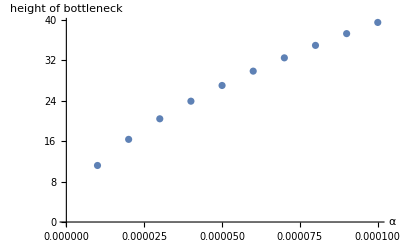

```mathematica
ListPlot[Transpose[{αValues,allBottleneckHeights}],AxesLabel->{α,"height of bottleneck"}]
```

```mathematica
commonICRules=commonIC/.(A_==B_)->(A->B);
```

```mathematica
analyticalHeights=(analyticalBottleneckHeight/.ninit->(n[0][0]/.commonICRules)/.f0->f[0]/.f1->f[1]/.η->η[1]/.commonRules/.α->#/.v->(9v[0]/.commonICRules)&)/@αValues;
```

```mathematica
analyticalHeights
```

{11.3776,15.5306,18.6312,21.1996,23.4332,25.4317,27.2538,28.9374,30.5085,31.9861}

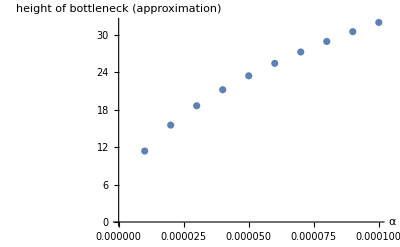

```mathematica
ListPlot[Transpose[{αValues,analyticalHeights}],AxesLabel->{α,"height of bottleneck (approximation)"}]
```

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.

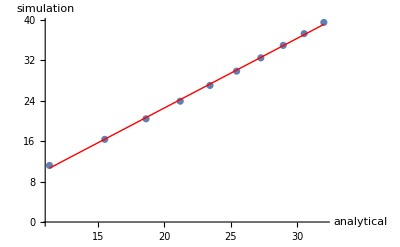

```mathematica
lstPlot=ListPlot[Transpose[{analyticalHeights, allBottleneckHeights}],AxesLabel->{"analytical","simulation"}];
model=LinearModelFit[Transpose[{analyticalHeights,allBottleneckHeights}],x,x];
fitPlot=Plot[model["BestFit"],{x,Min[analyticalHeights],Max[analyticalHeights]},PlotStyle->{Red,Thin}];
Show[lstPlot,fitPlot]
```

Optimal spacer distribution

```mathematica
rules={nsp->1,k->0,α[_]->0,f[_]->f};
```

```mathematica
eqns=createEquations[rules]
```

{n[0]'[t]==-g v[t] η[0] n[0][t]+f n[0][t] (1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop),nI[0]'[t]==g v[t] η[0] n[0][t]-μ nI[0][t],v'[t]==-g v[t] (n[0][t]+n[1][t])+b μ (nI[0][t]+nI[1][t]),n[1]'[t]==-g v[t] η[1] n[1][t]+f n[1][t] (1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop),nI[1]'[t]==g v[t] η[1] n[1][t]-μ nI[1][t]}

```mathematica
params={v[0]->{5 10^4,5 10^4},ninit->2 10^2,Kpop->2 10^4,g->10^-4,f->1,b->100,μ->1,failures->{{0.005, 0.5},{0.5, 0.005}},tmax->10};
```

```mathematica
ClearAll[getDoubleSolution];
getDoubleSolution[params_, pSpacer_?NumericQ]:=Module[{soln1,soln2,iniConds,fMat,sum},
iniConds=Table[{
n[0][0]==pSpacer (ninit/.params),
n[1][0]==(1-pSpacer)(ninit/.params),
nI[0][0]==0,
nI[1][0]==0,
v[0]==(v[0]/.params)[[i]]},
{i,1,2}];
fMat=(failures/.params);
soln1=NDSolve[Evaluate[Join[eqns/.params/.η[0]->(fMat[[1,1]])/.η[1]->(fMat[[2,1]]),iniConds[[1]]]],{n[0],n[1],nI[0],nI[1],v},{t,0,(tmax/.params)}];
soln2=NDSolve[Evaluate[Join[eqns/.params/.η[0]->(fMat[[1,2]])/.η[1]->(fMat[[2,2]]),iniConds[[1]]]],{n[0],n[1],nI[0],nI[1],v},{t,0,(tmax/.params)}];
(*sum=(n[0][#]+n[1][#]+nI[0][#]+nI[1][#]&);*)
sum=(n[0][#]+n[1][#]&);
{sum/.soln1[[1]],sum/.soln2[[1]],{soln1[[1]],soln2[[1]]}}
];
```

```mathematica
getBottleneck[soln_]:=FindMinimum[{soln[t],t>0},{t,5}][[1]];
```

```mathematica
ClearAll[getAverageBottleneck];
getAverageBottleneck[solns_,pVirus_?NumericQ]:=pVirus getBottleneck[solns[[1]]] + (1-pVirus)getBottleneck[solns[[2]]];
```

```mathematica
test=getDoubleSolution[params,0.1];
```

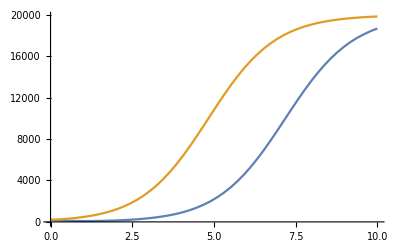

```mathematica
Plot[{test[[1]][t],test[[2]][t]},{t,0,(tmax/.params)},PlotRange->{0,Automatic}]
```

```mathematica
getAverageBottleneck[test,0.2]
```

176.86

```mathematica
getAverageBottleneckFromParams[params_,pSpacer_?NumericQ,pVirus_?NumericQ]:=getAverageBottleneck[getDoubleSolution[params,pSpacer],pVirus];
```

```mathematica
(*findBestSpacerDistribution[params_,pVirus_]:=FindMinimum[{-getAverageBottleneckFromParams[params,pSpacer,pVirus],pSpacer≥0,pSpacer≤1},{pSpacer,pVirus}];*)
```

```mathematica
values=Table[getAverageBottleneckFromParams[params,pSpacer,pVirus],{pSpacer,0,1,0.1},{pVirus,0,1,0.1}]
```

{{200.,180.,160.,140.,120.,100.,80.,60.,40.,20.,1.2734×10^-7},{200.,188.43,176.86,165.29,153.72,142.15,130.58,119.01,107.44,95.8705,84.3005},{200.,192.977,185.954,178.931,171.908,164.885,157.862,150.839,143.816,136.793,129.77},{200.,196.114,192.228,188.341,184.455,180.569,176.683,172.797,168.91,165.024,161.138},{199.958,198.199,196.439,194.68,192.921,191.162,189.403,187.644,185.885,184.126,182.367},{195.116,195.116,195.116,195.116,195.116,195.116,195.116,195.116,195.116,195.116,195.116},{182.367,184.126,185.885,187.644,189.403,191.162,192.921,194.68,196.439,198.199,199.958},{161.138,165.024,168.91,172.797,176.683,180.569,184.455,188.341,192.228,196.114,200.},{129.77,136.793,143.816,150.839,157.862,164.885,171.908,178.931,185.954,192.977,200.},{84.3005,95.8705,107.44,119.01,130.58,142.15,153.72,165.29,176.86,188.43,200.},{1.2734×10^-7,20.,40.,60.,80.,100.,120.,140.,160.,180.,200.}}

```mathematica
ListPlot3D[values,AxesLabel->{"pVirus","pSpacer"}]
```

-Graphics3D-

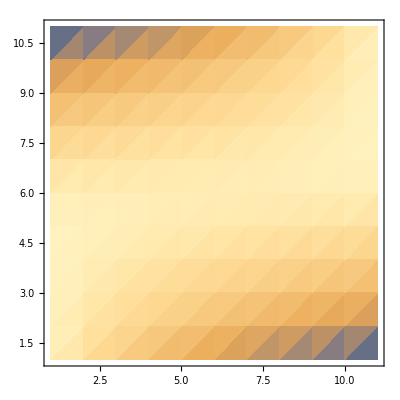

```mathematica
ListDensityPlot[values]
```

## Estimating error bars -- first try

```mathematica
eqns
```

{n[0]'[t]==-g v[t] η[0] n[0][t]+f n[0][t] (1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop),nI[0]'[t]==g v[t] η[0] n[0][t]-μ nI[0][t],v'[t]==-g v[t] (n[0][t]+n[1][t])+b μ (nI[0][t]+nI[1][t]),n[1]'[t]==-g v[t] η[1] n[1][t]+f n[1][t] (1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop),nI[1]'[t]==g v[t] η[1] n[1][t]-μ nI[1][t]}

```mathematica
testRules={vi->5 10^4,ni[0]->2 10^3,ni[1]->2 10^3,Kpop->2 10^4,g->10^-4,f->1,b->100,μ->1,η[0]->0.007, η[1]->0.02,tmax->40}
```

{vi→50000,ni[0]→2000,ni[1]→2000,Kpop→20000,g→1/10000,f→1,b→100,μ→1,η[0]→0.007,η[1]→0.02,tmax→40}

```mathematica
testSoln=NDSolve[Join[eqns/.testRules,{v[0]==(vi/.testRules),n[0][0]==(ni[0]/.testRules),n[1][0]==(ni[1]/.testRules),nI[0][0]==0,nI[1][0]==0}],{n[0],n[1],nI[0],nI[1],v},{t,0,(tmax/.testRules)}][[1]]
```

{n[0]→InterpolatingFunction[{{0., 40.}}, <>],n[1]→InterpolatingFunction[{{0., 40.}}, <>],nI[0]→InterpolatingFunction[{{0., 40.}}, <>],nI[1]→InterpolatingFunction[{{0., 40.}}, <>],v→InterpolatingFunction[{{0., 40.}}, <>]}

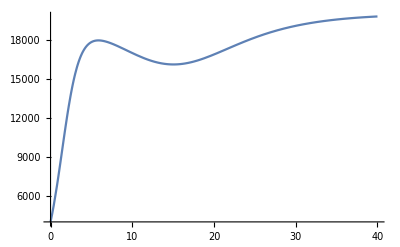

```mathematica
Plot[n[0][t]+n[1][t]/.testSoln,{t,0,(tmax/.testRules)},PlotRange->All]
```

```mathematica
testVar=NDSolve[Evaluate[{var[0]'[t]==f(1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop)+ η[0] g v[t],var[1]'[t]==f(1-(n[0][t]+n[1][t]+nI[0][t]+nI[1][t])/Kpop)+ η[1] g v[t],var[0][0]==0,var[1][0]==0}/.testRules/.testSoln],{var[0],var[1]},{t,0,(tmax/.testRules)}][[1]]
```

{var[0]→InterpolatingFunction[{{0., 40.}}, <>],var[1]→InterpolatingFunction[{{0., 40.}}, <>]}

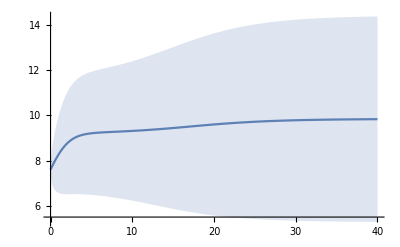

```mathematica
testPlotLogN0=Plot[Log[n[0][t]]/.testSoln,{t,0,(tmax/.testRules)},PlotRange->All];
testPlotLogN0Err=Plot[Evaluate[{Log[n[0][t]]-2Sqrt[var[0][t]],Log[n[0][t]]+2Sqrt[var[0][t]]}/.testSoln/.testVar],{t,0,(tmax/.testRules)},Filling->{1->{2}},PlotStyle->None];
Show[testPlotLogN0Err,testPlotLogN0]
```

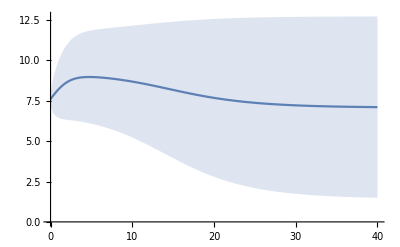

```mathematica
testPlotLogN1=Plot[Log[n[1][t]]/.testSoln,{t,0,(tmax/.testRules)},PlotRange->All];
testPlotLogN1Err=Plot[Evaluate[{Log[n[1][t]]-2 Sqrt[var[1][t]],Log[n[1][t]]+2Sqrt[var[1][t]]}/.testSoln/.testVar],{t,0,(tmax/.testRules)},Filling->{1->{2}},PlotStyle->None];
Show[testPlotLogN1Err,testPlotLogN1]
```

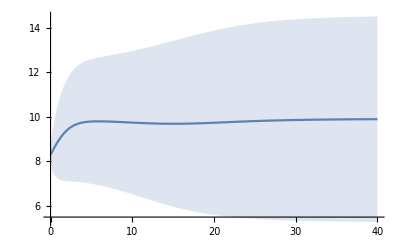

```mathematica
testPlotLogNtot=Plot[Log[n[0][t]+n[1][t]]/.testSoln,{t,0,(tmax/.testRules)},PlotRange->All];
testPlotLogNtotErr=Plot[Evaluate[{Log[n[0][t]+n[1][t]]-2(n[0][t]Sqrt[var[0][t]]+n[1][t]Sqrt[var[1][t]])/(n[0][t]+n[1][t]),Log[n[0][t]+n[1][t]]+2(n[0][t]Sqrt[var[0][t]]+n[1][t]Sqrt[var[1][t]])/(n[0][t]+n[1][t])}/.testSoln/.testVar],{t,0,(tmax/.testRules)},Filling->{1->{2}},PlotStyle->None];
Show[testPlotLogNtotErr,testPlotLogNtot]
```

```mathematica
CDF[NormalDistribution[9.5,4],0]
```

0.00877448